```mathematica
Import["https://www.faception.com", "Hyperlinks"]
```

{https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.linkedin.com/company/10588678?trk=vsrp_companies_res_name&trkInfo=VSRPsearchId%3A17333341461632536471%2CVSRPtargetId%3A10588678%2CVSRPcmpt%3Aprimary,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg,https://angel.co/faception,https://www.faception.com,https://www.faception.com,https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,http://demo.faception.com/demo/app,https://www.faception.com/about-us,https://www.faception.com/our-technology,https://www.faception.com/our-technology,https://www.faception.com/hls-and-public-safety,https://www.faception.com/personal-robots-1,https://www.faception.com/hls-and-public-safety,https://www.youtube.com/watch?v=p5pl6_zDgBk&feature=youtu.be,http://www.discovery.com/extra/adsales/ThisIsAI/,http://www.discovery.com/extra/adsales/ThisIsAI/,https://www.faception.com/news-events,https://i-hls.com/he/archives/83987,https://i-hls.com/archives/83984,https://i-hls.com/archives/73658,https://www.faception.com/news-events,http://www.securitychina.com.cn/,https://www.faception.com/news-events,https://asia.nikkei.com/Politics/International-Relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://www.faception.com/news-events,http://click.notice.ft.com/f/a/Mlm2JUCBbNXti2SVeJkuog~~/AAAAAQA~/RgRcwHWCP0RPaHR0cHM6Ly93d3cuZnQuY29tL2NvbnRlbnQvYjM4N2IxYTItZGU3Yi0xMWU3LWEwZDQtMDk0NGM1ZjQ5ZTQ2P3NoYXJldHlwZT1zaGFyZVcIZmludGltZXNYBAAAAABCCgABgvDdWrJqkExSEnNoYWlAZmFjZXB0aW9uLmNvbQ~~,http://israelhlscyber.com/}

```mathematica
StringStartsQ["lol","l"]
```

True

```mathematica
StringStartsQ[
Import["https://www.faception.com", "Hyperlinks"], "https://www.faception.com/"]
```

{True,True,True,True,True,False,False,False,False,False,True,True,True,True,True,False,True,True,True,True,True,True,False,False,False,True,False,False,False,True,False,True,False,True,False,False}

```mathematica
Select[
Import["https://www.faception.com", "Hyperlinks"],
StringStartsQ[
#,
 "https://www.faception.com/"]&]
```

{https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/about-us,https://www.faception.com/our-technology,https://www.faception.com/our-technology,https://www.faception.com/hls-and-public-safety,https://www.faception.com/personal-robots-1,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/news-events,https://www.faception.com/news-events,https://www.faception.com/news-events}

```mathematica
EntityClass["MilitaryConflict", "Properties"]
```

EntityClass[MilitaryConflict,Properties]

```mathematica
EntityList[EntityClass["MilitaryConflict","Properties"]]
```

Missing[UnknownEntityClass,{MilitaryConflict,Properties}]

```mathematica
test[arg_List]:=arg
```

```mathematica
test[4]
```

test[4]

```mathematica
test[{}]
```

{}

```mathematica
test[List[1]]
```

{1}

```mathematica
test[True]
```

test[True]

```mathematica
test2[arg_Integer]:=int
```

```mathematica
test2[1]
```

int

```mathematica
test2[arg_Integer]:=arg
```

```mathematica
test2[1]
```

1

```mathematica
test[1.1]
```

test[1.1]

```mathematica
test2@True
```

test2[True]

```mathematica
test2@{}
```

test2[{}]

```mathematica
Clear[test, test2]
```

```mathematica
Map[
Function[s,Select[
Import["https://www.faception.com", "Hyperlinks"],
StringStartsQ[
#,
 "https://www.faception.com/"]&]],{"https://www.faception.com"}]
```

{{https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/about-us,https://www.faception.com/our-technology,https://www.faception.com/our-technology,https://www.faception.com/hls-and-public-safety,https://www.faception.com/personal-robots-1,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/news-events,https://www.faception.com/news-events,https://www.faception.com/news-events}}

```mathematica
test[{a_List,b_Integer,c_String}]:={a,b,c}
```

```mathematica
test@{1,2,3}
```

test[{1,2,3}]

```mathematica
test[{{},1,""}]
```

{{},1,}

```mathematica
Clear@test
```

```mathematica
Join[Range@10,Range@5]
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

```mathematica
Union[Range@10,Range@5]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
ParallelTable[i, {i,1,100}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

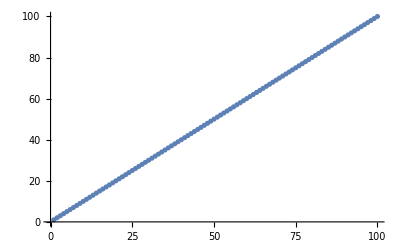

```mathematica
ListPlot[%27]
```

```mathematica
links[{raw_List,prefix_String,done_List}]:=With[{
result=Select[
ParallelMap[
Function[s,
Import[s, "Hyperlinks"]],
Complement[raw,done]],
StringStartsQ[#,prefix]&]
},{
Complement[result,raw],
prefix,
Union[done,raw]
}]
```

```mathematica
links[{raw_String, prefix_String}]:=links[{{raw},prefix,{}}]
```

```mathematica
links["https://www.faception.com/", "https://www.faception.com/"]
```

links[https://www.faception.com/,https://www.faception.com/]

```mathematica
links[raw_String, prefix_String]:=links[{raw,prefix}]
```

```mathematica
links["https://www.faception.com/", "https://www.faception.com/"]
```

{{},https://www.faception.com/,{https://www.faception.com/}}

```mathematica
Select[
ParallelMap[
Function[s,
Import[s, "Hyperlinks"]],
{"https://www.faception.com/"}],
StringStartsQ[#,"https://www.faception.com/"]&]
```

{}

```mathematica
ParallelMap[
Function[s,
Import[s, "Hyperlinks"]],
{"https://www.faception.com/"}]
```

{{https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.linkedin.com/company/10588678?trk=vsrp_companies_res_name&trkInfo=VSRPsearchId%3A17333341461632536471%2CVSRPtargetId%3A10588678%2CVSRPcmpt%3Aprimary,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg,https://angel.co/faception,https://www.faception.com,https://www.faception.com,https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,http://demo.faception.com/demo/app,https://www.faception.com/about-us,https://www.faception.com/our-technology,https://www.faception.com/our-technology,https://www.faception.com/hls-and-public-safety,https://www.faception.com/personal-robots-1,https://www.faception.com/hls-and-public-safety,https://www.youtube.com/watch?v=p5pl6_zDgBk&feature=youtu.be,http://www.discovery.com/extra/adsales/ThisIsAI/,http://www.discovery.com/extra/adsales/ThisIsAI/,https://www.faception.com/news-events,https://i-hls.com/he/archives/83987,https://i-hls.com/archives/83984,https://i-hls.com/archives/73658,https://www.faception.com/news-events,http://www.securitychina.com.cn/,https://www.faception.com/news-events,https://asia.nikkei.com/Politics/International-Relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://www.faception.com/news-events,http://click.notice.ft.com/f/a/Mlm2JUCBbNXti2SVeJkuog~~/AAAAAQA~/RgRcwHWCP0RPaHR0cHM6Ly93d3cuZnQuY29tL2NvbnRlbnQvYjM4N2IxYTItZGU3Yi0xMWU3LWEwZDQtMDk0NGM1ZjQ5ZTQ2P3NoYXJldHlwZT1zaGFyZVcIZmludGltZXNYBAAAAABCCgABgvDdWrJqkExSEnNoYWlAZmFjZXB0aW9uLmNvbQ~~,http://israelhlscyber.com/}}

```mathematica
Map[
Function[s,
Import[s, "Hyperlinks"]],
{"https://www.faception.com/"}]
```

{{https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.linkedin.com/company/10588678?trk=vsrp_companies_res_name&trkInfo=VSRPsearchId%3A17333341461632536471%2CVSRPtargetId%3A10588678%2CVSRPcmpt%3Aprimary,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg,https://angel.co/faception,https://www.faception.com,https://www.faception.com,https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,http://demo.faception.com/demo/app,https://www.faception.com/about-us,https://www.faception.com/our-technology,https://www.faception.com/our-technology,https://www.faception.com/hls-and-public-safety,https://www.faception.com/personal-robots-1,https://www.faception.com/hls-and-public-safety,https://www.youtube.com/watch?v=p5pl6_zDgBk&feature=youtu.be,http://www.discovery.com/extra/adsales/ThisIsAI/,http://www.discovery.com/extra/adsales/ThisIsAI/,https://www.faception.com/news-events,https://i-hls.com/he/archives/83987,https://i-hls.com/archives/83984,https://i-hls.com/archives/73658,https://www.faception.com/news-events,http://www.securitychina.com.cn/,https://www.faception.com/news-events,https://asia.nikkei.com/Politics/International-Relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://www.faception.com/news-events,http://click.notice.ft.com/f/a/Mlm2JUCBbNXti2SVeJkuog~~/AAAAAQA~/RgRcwHWCP0RPaHR0cHM6Ly93d3cuZnQuY29tL2NvbnRlbnQvYjM4N2IxYTItZGU3Yi0xMWU3LWEwZDQtMDk0NGM1ZjQ5ZTQ2P3NoYXJldHlwZT1zaGFyZVcIZmludGltZXNYBAAAAABCCgABgvDdWrJqkExSEnNoYWlAZmFjZXB0aW9uLmNvbQ~~,http://israelhlscyber.com/}}

```mathematica
Select[
Join@ParallelMap[
Function[s,
Import[s, "Hyperlinks"]],
{"https://www.faception.com/"}],
StringStartsQ[#,"https://www.faception.com/"]&]
```

{}

```mathematica
Select[
Flatten[
ParallelMap[
Function[s,
Import[s, "Hyperlinks"]],
{"https://www.faception.com/"}],1],
StringStartsQ[#,"https://www.faception.com/"]&]
```

{https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/our-technology,https://www.faception.com/about-us,https://www.faception.com/news-events,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/about-us,https://www.faception.com/our-technology,https://www.faception.com/our-technology,https://www.faception.com/hls-and-public-safety,https://www.faception.com/personal-robots-1,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/news-events,https://www.faception.com/news-events,https://www.faception.com/news-events}

```mathematica
links[{raw_List,prefix_String,done_List}]:=With[{
result=Select[
Flatten[
ParallelMap[
Function[s,
Import[s, "Hyperlinks"]],
Complement[raw,done]],
StringStartsQ[#,prefix]&]
},{
Complement[result,raw],
prefix,
Union[done,raw]
}]
```

```mathematica
Flatten[
ParallelMap[
Select[
Function[s,
Import[s, "Hyperlinks"]],
{"https://www.faception.com/"}],
StringStartsQ[#,"https://www.faception.com/"]&],1]
```

Import::chtype: First argument s is not a valid file, directory, or URL specification.

Function::argb: Function called with 0 arguments; between 1 and 3 arguments are expected.

Function[][StringStartsQ[#1,https://www.faception.com/]]&

```mathematica
links[{raw_List,prefix_String,done_List}]:=With[{
result=Select[
Flatten[
ParallelMap[
Function[s,
Import[s, "Hyperlinks"]],
Complement[raw,done]],
1],
StringStartsQ[#,prefix]&]
},{
Complement[result,raw],
prefix,
Union[done,raw]
}]
```

```mathematica
links["https://www.faception.com/", "https://www.faception.com/"]
```

{{https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/our-technology,https://www.faception.com/personal-robots-1},https://www.faception.com/,{https://www.faception.com/}}

```mathematica
Nest[f,x,3]
```

f[f[f[x]]]

```mathematica
Nest[links,"https://www.faception.com/",
```

```mathematica
links[ss_String]:=links[ss,ss]
```

```mathematica
Nest[links,"https://www.faception.com/",0]
```

https://www.faception.com/

```mathematica
Nest[links,"https://www.faception.com/",1]
```

link[https://www.faception.com/,https://www.faception.com/]

```mathematica
Nest[links,"https://www.faception.com/",1]
```

{{https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/our-technology,https://www.faception.com/personal-robots-1},https://www.faception.com/,{https://www.faception.com/}}

```mathematica
Nest[links,"https://www.faception.com/",2]
```

{{https://www.faception.com/events,https://www.faception.com/press-kit,https://www.faception.com/single-post/2016/05/09/Can-technology-predict-who-will-win-a-poker-tournament,https://www.faception.com/single-post/2016/05/29/Demo-Day-was-a-blast-and-marked-an-exciting-month-for-Faception-1,https://www.faception.com/single-post/2016/06/03/More-than-20-articles-covering-Faception},https://www.faception.com/,{https://www.faception.com/,https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/our-technology,https://www.faception.com/personal-robots-1}}

```mathematica
Nest[links,"https://www.faception.com/",3]
```

{{https://www.faception.com/,https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/news-events,https://www.faception.com/our-technology},https://www.faception.com/,{https://www.faception.com/,https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/events,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/our-technology,https://www.faception.com/personal-robots-1,https://www.faception.com/press-kit,https://www.faception.com/single-post/2016/05/09/Can-technology-predict-who-will-win-a-poker-tournament,https://www.faception.com/single-post/2016/05/29/Demo-Day-was-a-blast-and-marked-an-exciting-month-for-Faception-1,https://www.faception.com/single-post/2016/06/03/More-than-20-articles-covering-Faception}}

```mathematica
Nest[links,"https://www.faception.com/",4]
```

{{},https://www.faception.com/,{https://www.faception.com/,https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/events,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/our-technology,https://www.faception.com/personal-robots-1,https://www.faception.com/press-kit,https://www.faception.com/single-post/2016/05/09/Can-technology-predict-who-will-win-a-poker-tournament,https://www.faception.com/single-post/2016/05/29/Demo-Day-was-a-blast-and-marked-an-exciting-month-for-Faception-1,https://www.faception.com/single-post/2016/06/03/More-than-20-articles-covering-Faception}}

```mathematica
StringStartsQ["fjsdlkfjsd", ""]
```

True

```mathematica
Nest[links,{"https://www.faception.com/", "", {}},1]
```

links[{https://www.faception.com/,,{}}]

```mathematica
Nest[links,{{"https://www.faception.com/"}, "", {}},1]
```

{{http://click.notice.ft.com/f/a/Mlm2JUCBbNXti2SVeJkuog~~/AAAAAQA~/RgRcwHWCP0RPaHR0cHM6Ly93d3cuZnQuY29tL2NvbnRlbnQvYjM4N2IxYTItZGU3Yi0xMWU3LWEwZDQtMDk0NGM1ZjQ5ZTQ2P3NoYXJldHlwZT1zaGFyZVcIZmludGltZXNYBAAAAABCCgABgvDdWrJqkExSEnNoYWlAZmFjZXB0aW9uLmNvbQ~~,http://demo.faception.com/demo/app,http://israelhlscyber.com/,https://angel.co/faception,https://asia.nikkei.com/Politics/International-Relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://i-hls.com/archives/73658,https://i-hls.com/archives/83984,https://i-hls.com/he/archives/83987,https://www.faception.com,https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/our-technology,https://www.faception.com/personal-robots-1,https://www.linkedin.com/company/10588678?trk=vsrp_companies_res_name&trkInfo=VSRPsearchId%3A17333341461632536471%2CVSRPtargetId%3A10588678%2CVSRPcmpt%3Aprimary,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg,https://www.youtube.com/watch?v=p5pl6_zDgBk&feature=youtu.be,http://www.discovery.com/extra/adsales/ThisIsAI/,http://www.securitychina.com.cn/},,{https://www.faception.com/}}

```mathematica
Length@Out@54
```

3

```mathematica
Nest[links,{{"https://www.faception.com/"}, "", {}},2]
```

FetchURL::httperr: The request to URL https://angel.co/faception was not successful. The server returned the HTTP status code 403 ("Forbidden").

FetchURL::httperr: The request to URL https://www.linkedin.com/company/10588678?trk=vsrp_companies_res_name&trkInfo=VSRPsearchId%3A17333341461632536471%2CVSRPtargetId%3A10588678%2CVSRPcmpt%3Aprimary was not successful. The server returned the HTTP status code 999.

FetchURL::httperr: The request to URL http://www.discovery.com/extra/adsales/ThisIsAI/ was not successful. The server returned the HTTP status code 404 ("Not Found").

FetchURL::conopen: The connection to URL http://demo.faception.com/demo/app cannot be opened. If the URL is correct, you might need to configure your firewall program, or you might need to set a proxy in the Internet connectivity tab of the Preferences dialog (or by calling SetInternetProxy).  For HTTPS connections, you might need to inspect the authenticity of the server's SSL certificate and choose to accept it.

StringStartsQ::strse: String or list of strings expected at position 1 in StringStartsQ[$Failed,].

General::stop: Further output of StringStartsQ::strse will be suppressed during this calculation.

{{/Business/Technology/Toyota-IBM-and-more-push-for-global-data-security-ahead-of-G-20,/Economy/Trade-war/Australia-urges-US-and-China-to-resolve-trade-war,/Economy/Trade-war/Trump-calls-off-tariffs-on-Mexico-after-deal-on-migration,/Editor-s-Picks/China-up-close,/Editor-s-Picks/China-up-close/Behind-China-s-sudden-olive-branch-to-Japan,http://aboutus.ft.com/en-gb/ft-editorial-code/,http://conteudo.startse.com.br/mundo/michel-bekhor/startse-em-israel-reconhecimento-facial-acerta-92-dos-terroristas/,http://defense-update.com/20161212_accelerator_graduation.html,http://ft.com/more-from-ft-group,http://fttoolkit.co.uk/,http://help.ft.com,http://help.ft.com/help/legal-privacy/cookies/,http://help.ft.com/help/legal-privacy/copyright/copyright-policy/,http://help.ft.com/help/legal-privacy/privacy/,http://help.ft.com/help/legal-privacy/terms-conditions/,http://live.ft.com/,http://markets.ft.com/data/alerts/,http://mobil.n-tv.de/mediathek/sendungen/Start_up_News/Zu-Besuch-im-Gruender-Wunder-Tel-Aviv-article18292991.html,http://mp.weixin.qq.com/s?__biz=MzAxMDM3NTM0OA==&mid=2648766367&idx=1&sn=40adea8243eee06b07941ea7d3cd2682&scene=5&srcid=0908VYnRhqwQWdpwhOmu21xU#rd,http://rankings.ft.com/businessschoolrankings/global-mba-ranking-2019,http://rankings.ft.com/businessschoolrankings/rankings,https://aboutus.ft.com/en-gb/careers/,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26feature%3Dplaylist%26next%3D%252Fchannel%252FUC4soZq4VUNgTUhVhPKB1dSg%26hl%3Den&service=youtube&uilel=3&hl=en,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26feature%3Dsign_in_promo%26next%3D%252Fchannel%252FUC4soZq4VUNgTUhVhPKB1dSg%26hl%3Den&service=youtube&uilel=3&hl=en,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26next%3D%252Fwatch%253Fv%253Dp5pl6_zDgBk%2526feature%253Dyoutu.be%26hl%3Den%26feature%3D__FEATURE__&service=youtube&hl=en&uilel=3,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26next%3D%252Fwatch%253Fv%253Dp5pl6_zDgBk%2526feature%253Dyoutu.be%26hl%3Den%26feature%3Dplaylist&service=youtube&hl=en&uilel=3,https://asia.nikkei.com/Asia300,https://asia.nikkei.com/Business,https://asia.nikkei.com/Business/Aerospace-Defense,https://asia.nikkei.com/Business/Automobile,https://asia.nikkei.com/Business/Banking-Finance,https://asia.nikkei.com/Business/Biotechnology,https://asia.nikkei.com/Business/Construction,https://asia.nikkei.com/Business/Consumer,https://asia.nikkei.com/Business/Electronics,https://asia.nikkei.com/Business/Energy,https://asia.nikkei.com/Business/Food-Beverage,https://asia.nikkei.com/Business/Health-Care,https://asia.nikkei.com/Business/Hotels-Restaurants-Leisure,https://asia.nikkei.com/Business/Insurance,https://asia.nikkei.com/Business/Machinery-Industrial-Equipment,https://asia.nikkei.com/Business/Markets,https://asia.nikkei.com/Business/Materials,https://asia.nikkei.com/Business/Media-Entertainment,https://asia.nikkei.com/Business/Pharmaceuticals,https://asia.nikkei.com/Business/Real-Estate,https://asia.nikkei.com/Business/Retail,https://asia.nikkei.com/Business/Services,https://asia.nikkei.com/Business/Technology,https://asia.nikkei.com/Business/Telecommunication,https://asia.nikkei.com/Business/Transportation,https://asia.nikkei.com/Economy,https://asia.nikkei.com/Editor-s-Picks,https://asia.nikkei.com/info/rss,https://asia.nikkei.com/Life-Arts,https://asia.nikkei.com/Location/East-Asia,https://asia.nikkei.com/Location/East-Asia/China,https://asia.nikkei.com/Location/East-Asia/Japan,https://asia.nikkei.com/Location/Rest-of-the-World,https://asia.nikkei.com/Location/South-Asia,https://asia.nikkei.com/Location/South-Asia/India,https://asia.nikkei.com/Location/Southeast-Asia,https://asia.nikkei.com/Location/Southeast-Asia/ASEAN,https://asia.nikkei.com/Opinion,https://asia.nikkei.com/Politics,https://asia.nikkei.com/Politics/Japan-s-Abe-rolls-out-red-carpet-for-Trump,https://asia.nikkei.com/Politics/Japan-to-introduce-facial-recognition-for-departing-foreigners,https://asia.nikkei.com/Spotlight/Trump-Xi-Summit/Tang-poems-and-folk-tales-History-s-role-in-the-Trump-Xi-reset,https://ausr.i-hls.com/,https://ausr.i-hls.com/he,https://consent.ft.com/__consent/consent-record-cookie?redirect=https://www.ft.com,https://docs.wixstatic.com/ugd/a4ba41_efc9468fd9754aaa961540cc145a79b6.pdf,http://security.qianjia.com,https://enterprise.ft.com/en-gb/services/group-subscriptions/education/,https://enterprise.ft.com/en-gb/services/group-subscriptions/group-contact-us/?segmentId=383c7f63-abf4-b62d-cb33-4c278e6fdf61&cpccampaign=B2B_link_ft.com_footer,https://enterprise.ft.com/en-gb/services/republishing/,https://ftalphaville.ft.com,https://help.ft.com/help/legal/slavery-statement/,https://howtospendit.ft.com/,https://i-hls.com,https://i-hls.com/,https://i-hls.com/about-i-hls,https://i-hls.com/accelerator,https://i-hls.com/advisory-board,https://i-hls.com/archives/72506,https://i-hls.com/archives/73659,https://i-hls.com/archives/76400,https://i-hls.com/archives/76609,https://i-hls.com/archives/76612,https://i-hls.com/archives/80237,https://i-hls.com/archives/80466,https://i-hls.com/archives/80591,https://i-hls.com/archives/80725,https://i-hls.com/archives/80737,https://i-hls.com/archives/80788,https://i-hls.com/archives/80801,https://i-hls.com/archives/80821,https://i-hls.com/archives/80826,https://i-hls.com/archives/80829,https://i-hls.com/archives/80841,https://i-hls.com/archives/80857,https://i-hls.com/archives/80866,https://i-hls.com/archives/80869,https://i-hls.com/archives/80873,https://i-hls.com/archives/80887,https://i-hls.com/archives/80893,https://i-hls.com/archives/8337,https://i-hls.com/archives/89191,https://i-hls.com/archives/89396,https://i-hls.com/archives/89801,https://i-hls.com/archives/90406,https://i-hls.com/archives/91114,https://i-hls.com/archives/91360,https://i-hls.com/archives/91511,https://i-hls.com/archives/91710,https://i-hls.com/archives/91863,https://i-hls.com/archives/91870,https://i-hls.com/archives/91871,https://i-hls.com/archives/91876,https://i-hls.com/archives/91882,https://i-hls.com/archives/91895,https://i-hls.com/archives/91901,https://i-hls.com/archives/91906,https://i-hls.com/archives/91913,https://i-hls.com/archives/91917,https://i-hls.com/archives/91923,https://i-hls.com/archives/91930,https://i-hls.com/archives/91937,https://i-hls.com/archives/91945,https://i-hls.com/archives/91950,https://i-hls.com/archives/91959,https://i-hls.com/archives/91966,https://i-hls.com/archives/91971,https://i-hls.com/archives/91977,https://i-hls.com/archives/91982,https://i-hls.com/archives/91990,https://i-hls.com/archives/author,https://i-hls.com/cdn-cgi/l/email-protection#0964687d686749602461657a276a6664,https://i-hls.com/cdn-cgi/l/email-protection#1d74737b725d743075716e337e7270,https://i-hls.com/cdn-cgi/l/email-protection#89e4e8fde8e7c9e0a4e1e5faa7eae6e4,https://i-hls.com/cdn-cgi/l/email-protection#b3daddd5dcf3da9edbdfc09dd0dcde,https://i-hls.com/contact-us,https://i-hls.com/events2016,https://i-hls.com/events/offshoreperimiter2015/,https://i-hls.com/events/offshoreperimiter2015/he/,https://i-hls.com/events/pioneer/,https://i-hls.com/events/pioneer/he/,https://i-hls.com/events/pioneer/?lang=he,https://i-hls.com/?feed=rss,https://i-hls.com/he,https://i-hls.com/he/66597-2,https://i-hls.com/he/78613-2,https://i-hls.com/he/about-i-hls,https://i-hls.com/he/archives/51772,https://i-hls.com/he/archives/59687,https://i-hls.com/he/archives/61961,https://i-hls.com/he/archives/72504,https://i-hls.com/he/archives/80727,https://i-hls.com/he/archives/80739,https://i-hls.com/he/archives/80760,https://i-hls.com/he/archives/80775,https://i-hls.com/he/archives/80799,https://i-hls.com/he/archives/80804,https://i-hls.com/he/archives/80830,https://i-hls.com/he/archives/80833,https://i-hls.com/he/archives/80844,https://i-hls.com/he/archives/80850,https://i-hls.com/he/archives/80868,https://i-hls.com/he/archives/80871,https://i-hls.com/he/archives/80880,https://i-hls.com/he/archives/80883,https://i-hls.com/he/archives/80889,https://i-hls.com/he/archives/80896,https://i-hls.com/he/archives/80903,https://i-hls.com/he/archives/89352,https://i-hls.com/he/archives/89507,https://i-hls.com/he/archives/89802,https://i-hls.com/he/archives/90124,https://i-hls.com/he/archives/90963,https://i-hls.com/he/archives/91100,https://i-hls.com/he/archives/91364,https://i-hls.com/he/archives/91831,https://i-hls.com/he/archives/91867,https://i-hls.com/he/archives/91875,https://i-hls.com/he/archives/91880,https://i-hls.com/he/archives/91888,https://i-hls.com/he/archives/91894,https://i-hls.com/he/archives/91900,https://i-hls.com/he/archives/91905,https://i-hls.com/he/archives/91910,https://i-hls.com/he/archives/91916,https://i-hls.com/he/archives/91921,https://i-hls.com/he/archives/91929,https://i-hls.com/he/archives/91936,https://i-hls.com/he/archives/91941,https://i-hls.com/he/archives/91949,https://i-hls.com/he/archives/91954,https://i-hls.com/he/archives/91964,https://i-hls.com/he/archives/91970,https://i-hls.com/he/archives/91975,https://i-hls.com/he/archives/91981,https://i-hls.com/he/archives/91986,https://i-hls.com/he/archives/91994,https://i-hls.com/he/archives/author,https://i-hls.com/he/%d7%94%d7%a8%d7%a9%d7%9e%d7%94-%d7%9c%d7%a0%d7%99%d7%95%d7%96%d7%9c%d7%98%d7%a8,https://i-hls.com/he/%d7%a6%d7%95%d7%a8-%d7%a7%d7%a9%d7%a8,https://i-hls.com/he/?feed=rss,https://i-hls.com/he/iHLS/%d7%90%d7%99%d7%a8%d7%95%d7%a2%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%90%d7%a7%d7%a1%d7%9c%d7%a8%d7%98%d7%95%d7%a8,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/%d7%99%d7%93%d7%99%d7%a2%d7%95%d7%aa-%d7%95%d7%99%d7%93%d7%90%d7%95,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/%d7%9e%d7%94%d7%93%d7%95%d7%a8%d7%94-%d7%95%d7%99%d7%93%d7%90%d7%95-%d7%a9%d7%91%d7%95%d7%a2%d7%99%d7%aa,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/interview-3,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/special-edition-3,https://i-hls.com/he/iHLS/%d7%96%d7%99%d7%94%d7%95%d7%99-%d7%a4%d7%a0%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%97%d7%91%d7%a8%d7%95%d7%aa,https://i-hls.com/he/iHLS/%d7%97%d7%93%d7%a9%d7%95%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%25d7%259b%25d7%2595%25d7%2597%25d7%2595%25d7%25aa-%25d7%25a2%25d7%25aa%25d7%2599%25d7%2593%25d7%2599%25d7%2599%25d7%259d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/ar-vr-mr,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/big-data-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%91%d7%99%d7%a0%d7%94-%d7%9e%d7%9c%d7%90%d7%9b%d7%95%d7%aa%d7%99%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%91%d7%99%d7%a0%d7%94-%d7%9e%d7%9c%d7%90%d7%9b%d7%95%d7%aa%d7%99%d7%aa/%d7%9c%d7%9e%d7%99%d7%93%d7%94-%d7%a2%d7%9e%d7%95%d7%a7%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%91%d7%99%d7%a0%d7%94-%d7%9e%d7%9c%d7%90%d7%9b%d7%95%d7%aa%d7%99%d7%aa/%d7%9c%d7%9e%d7%99%d7%93%d7%aa-%d7%9e%d7%9b%d7%95%d7%a0%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%94%d7%90%d7%99%d7%a0%d7%98%d7%a8%d7%a0%d7%98-%d7%a9%d7%9c-%d7%94%d7%93%d7%91%d7%a8%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa-%d7%9e%d7%92%d7%a0%d7%99%d7%91%d7%95%d7%aa-%d7%95%d7%92%d7%90%d7%93%d7%92%d7%98%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%9b%d7%9c%d7%99-%d7%98%d7%99%d7%a1,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%9e%d7%95%d7%93%d7%99%d7%a2%d7%99%d7%9f-%d7%9e%d7%a2%d7%a7%d7%91-%d7%95%d7%a1%d7%99%d7%95%d7%a8/%d7%9e%d7%95%d7%93%d7%99%d7%a2%d7%99%d7%9f,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%9e%d7%95%d7%93%d7%99%d7%a2%d7%99%d7%9f-%d7%9e%d7%a2%d7%a7%d7%91-%d7%95%d7%a1%d7%99%d7%95%d7%a8/surveillance-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a1%d7%99%d7%99%d7%91%d7%a8-2,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a1%d7%99%d7%99%d7%91%d7%a8-2/cyber_security-2,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a1%d7%99%d7%99%d7%91%d7%a8-2/%d7%a4%d7%a9%d7%99%d7%a2%d7%aa-%d7%a1%d7%99%d7%99%d7%91%d7%a8,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94/%d7%a2%d7%99%d7%a8-%d7%91%d7%98%d7%95%d7%97%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a7%d7%95%d7%95%d7%90%d7%a0%d7%98%d7%95%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%aa%d7%a7%d7%99%d7%a0%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%aa%d7%a7%d7%a9%d7%95%d7%a8%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/electro-optics-4,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/explosive1-detection-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/forensic-4,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%90%d7%a0%d7%98%d7%99-%d7%9b%d7%98%d7%91%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%91%d7%9c%d7%95%d7%9f,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%9b%d7%9c%d7%99-%d7%98%d7%99%d7%99%d7%a1,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%9b%d7%9c%d7%99%d7%9d-%d7%a7%d7%a8%d7%a7%d7%a2%d7%99%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%9b%d7%9c%d7%99-%d7%a9%d7%99%d7%99%d7%98,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%a6%d7%99%d7%95%d7%95%d7%aa-%d7%90%d7%93%d7%9d-%d7%9e%d7%9b%d7%95%d7%a0%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/sensors-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/sensors-3/%d7%9e%d7%a6%d7%9c%d7%9e%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/sensors-3/radar1-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/technology-news-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/wearable-technology-2,https://i-hls.com/he/iHLS/%d7%a0%d7%95%d7%a9%d7%90%d7%99%d7%9d-%d7%97%d7%9e%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%99%d7%a8%d7%90%d7%9f,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%99%d7%a8%d7%95%d7%a4%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%a4%d7%a8%d7%99%d7%a7%d7%94-he,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%a8%d7%94%d7%91-he,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%91%d7%a8%d7%96%d7%99%d7%9c,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%93%d7%a8%d7%95%d7%9d-%d7%90%d7%9e%d7%a8%d7%99%d7%a7%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%99%d7%a9%d7%a8%d7%90%d7%9c,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%a1%d7%95%d7%a8%d7%99%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%a1%d7%99%d7%9f,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%a8%d7%95%d7%a1%d7%99%d7%94-he,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/%d7%93%d7%91%d7%a8-%d7%94%d7%a2%d7%95%d7%a8%d7%9a,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/%d7%94%d7%9e%d7%9b%d7%95%d7%9f-%d7%9c%d7%9e%d7%93%d7%99%d7%a0%d7%99%d7%95%d7%aa-%d7%a0%d7%92%d7%93-%d7%98%d7%a8%d7%95%d7%a8,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/%d7%9e%d7%90%d7%9e%d7%a8%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/opinions-3,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%9e%d7%95%d7%a6%d7%a8%d7%99%d7%9d-%d7%97%d7%93%d7%a9%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/inss-2,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/inss-2/%d7%9c%d7%95%d7%97%d7%9e%d7%aa-%d7%a1%d7%99%d7%99%d7%91%d7%a8-inss,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/inss-2/%d7%a6%d7%91%d7%90-%d7%95%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%94,https://i-hls.com/he/iHLS/security-3,https://i-hls.com/he/iHLS/security-3/aviation_security-2,https://i-hls.com/he/iHLS/security-3/aviation_security-2/aircraft_security-2,https://i-hls.com/he/iHLS/security-3/coastal_security-2,https://i-hls.com/he/iHLS/security-3/counter-terror-4,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/airport1-security-he,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/%d7%90%d7%91%d7%98%d7%97%d7%aa-%d7%90%d7%99%d7%a8%d7%95%d7%a2%d7%99-%d7%a2%d7%a0%d7%a7,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/%d7%90%d7%91%d7%98%d7%97%d7%aa-%d7%9e%d7%aa%d7%a7%d7%a0%d7%99-%d7%90%d7%a0%d7%a8%d7%92%d7%99%d7%94,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/%d7%91%d7%aa%d7%99-%d7%9b%d7%9c%d7%90,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/infrastructure_security-2,https://i-hls.com/he/iHLS/security-3/%d7%93%d7%90%d7%a2%d7%a9,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%92%d7%a0%d7%94-%d7%9e%d7%a4%d7%a0%d7%99-%d7%90%d7%99%d7%95%d7%9e%d7%99%d7%9d-%d7%90%d7%95%d7%95%d7%99%d7%a8%d7%99%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%9e%d7%a9%d7%9b%d7%99%d7%95%d7%aa-%d7%91%d7%97%d7%a8%d7%95%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%9e%d7%a9%d7%9b%d7%99%d7%95%d7%aa-%d7%91%d7%97%d7%a8%d7%95%d7%9d/civil_defense-2,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%9e%d7%a9%d7%9b%d7%99%d7%95%d7%aa-%d7%91%d7%97%d7%a8%d7%95%d7%9d/disaster-recovery-3,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/cbrne-2,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/%d7%9e%d7%a2%d7%a8%d7%9b%d7%95%d7%aa-%d7%97%d7%99%d7%a8,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/%d7%a0%d7%a9%d7%a7-%d7%a2%d7%a9%d7%94-%d7%96%d7%90%d7%aa-%d7%91%d7%a2%d7%a6%d7%9e%d7%9a,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/%d7%a6%d7%99%d7%95%d7%93-%d7%90%d7%99%d7%a9%d7%99,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/firearms-3,https://i-hls.com/he/iHLS/security-3/first_responders-2,https://i-hls.com/he/iHLS/security-3/first_responders-2/law_enforcement-2,https://i-hls.com/he/iHLS/security-3/hls-he2,https://i-hls.com/he/iHLS/security-3/maritime_security-2,https://i-hls.com/he/iHLS/security-3/perimeter-3,https://i-hls.com/he/iHLS/security-3/perimeter-3/access_control-2,https://i-hls.com/he/iHLS/security-3/perimeter-3/biometric-3,https://i-hls.com/he/iHLS/security-3/perimeter-3/border_security-2,https://i-hls.com/he/iHLS/security-3/perimeter-3/port_security-2,https://i-hls.com/he/iHLS/security-3/public_transport-2,https://i-hls.com/he/iHLS/startup-he,https://i-hls.com/he/our-team,https://i-hls.com/iHLS/cbs,https://i-hls.com/iHLS/companies,https://i-hls.com/iHLS/events-3,https://i-hls.com/iHLS/ihls-accelerator,https://i-hls.com/iHLS/more,https://i-hls.com/iHLS/more/geo-politics,https://i-hls.com/iHLS/more/geo-politics/africa-2,https://i-hls.com/iHLS/more/geo-politics/brazil,https://i-hls.com/iHLS/more/geo-politics/china,https://i-hls.com/iHLS/more/geo-politics/europe,https://i-hls.com/iHLS/more/geo-politics/iran,https://i-hls.com/iHLS/more/geo-politics/israel,https://i-hls.com/iHLS/more/geo-politics/russia-2,https://i-hls.com/iHLS/more/geo-politics/south-america,https://i-hls.com/iHLS/more/geo-politics/syria,https://i-hls.com/iHLS/more/geo-politics/usa-defense-update,https://i-hls.com/iHLS/more/inss/cyber-warfare-program,https://i-hls.com/iHLS/more/inss/military-strategic-affairs,https://i-hls.com/iHLS/more/new-products,https://i-hls.com/iHLS/more/point-of-view,https://i-hls.com/iHLS/more/point-of-view/articles,https://i-hls.com/iHLS/more/point-of-view/editorial,https://i-hls.com/iHLS/more/point-of-view/ict,https://i-hls.com/iHLS/more/point-of-view/opinions,https://i-hls.com/iHLS/news,https://i-hls.com/iHLS/security,https://i-hls.com/iHLS/security/aviation_security,https://i-hls.com/iHLS/security/aviation_security/aircraft_security,https://i-hls.com/iHLS/security/bcp,https://i-hls.com/iHLS/security/bcp/civil_defense,https://i-hls.com/iHLS/security/bcp/disaster-recovery,https://i-hls.com/iHLS/security/bmd,https://i-hls.com/iHLS/security/coastal_security,https://i-hls.com/iHLS/security/counter-terror,https://i-hls.com/iHLS/security/first_responders,https://i-hls.com/iHLS/security/first_responders/law_enforcement,https://i-hls.com/iHLS/security/hls1,https://i-hls.com/iHLS/security/isis,https://i-hls.com/iHLS/security/maritime_security,https://i-hls.com/iHLS/security/perimeter,https://i-hls.com/iHLS/security/perimeter/access_control,https://i-hls.com/iHLS/security/perimeter/biometric,https://i-hls.com/iHLS/security/perimeter/border_security,https://i-hls.com/iHLS/security/perimeter/port_security,https://i-hls.com/iHLS/security/public_transport,https://i-hls.com/iHLS/security/strategic-sites,https://i-hls.com/iHLS/security/strategic-sites/airport-security-aviation_security,https://i-hls.com/iHLS/security/strategic-sites/energy,https://i-hls.com/iHLS/security/strategic-sites/infrastructure_security,https://i-hls.com/iHLS/security/strategic-sites/mega_events,https://i-hls.com/iHLS/security/strategic-sites/prisons,https://i-hls.com/iHLS/security/weapons,https://i-hls.com/iHLS/security/weapons/cbrne,https://i-hls.com/iHLS/security/weapons/do-it-yourself-weapons,https://i-hls.com/iHLS/security/weapons/firearms,https://i-hls.com/iHLS/security/weapons/infantry-systems,https://i-hls.com/iHLS/security/weapons/personal,https://i-hls.com/iHLS/startup,https://i-hls.com/iHLS/technology,https://i-hls.com/iHLS/technology/aircraft,https://i-hls.com/iHLS/technology/artificial-intelligence,https://i-hls.com/iHLS/technology/artificial-intelligence/deep-learning,https://i-hls.com/iHLS/technology/artificial-intelligence/machine-learning,https://i-hls.com/iHLS/technology/arvrmr,https://i-hls.com/iHLS/technology/big-data-2,https://i-hls.com/iHLS/technology/biometric-technology,https://i-hls.com/iHLS/technology/biometric-technology/facial-recognition,https://i-hls.com/iHLS/technology/communications,https://i-hls.com/iHLS/technology/cool-tech-and-gadgets,https://i-hls.com/iHLS/technology/cyber-2,https://i-hls.com/iHLS/technology/cyber-2/cyber-crime,https://i-hls.com/iHLS/technology/cyber-2/cyber_security,https://i-hls.com/iHLS/technology/cyber-2/cyber_security/blockchain,https://i-hls.com/iHLS/technology/electro-optics,https://i-hls.com/iHLS/technology/explosive_detection,https://i-hls.com/iHLS/technology/forensic,https://i-hls.com/iHLS/technology/future-forces,https://i-hls.com/iHLS/technology/internet-of-things,https://i-hls.com/iHLS/technology/isr/intelligence,https://i-hls.com/iHLS/technology/isr/surveillance,https://i-hls.com/iHLS/technology/itl,https://i-hls.com/iHLS/technology/quantum,https://i-hls.com/iHLS/technology/robotic,https://i-hls.com/iHLS/technology/robotic/aerostat,https://i-hls.com/iHLS/technology/robotic/anti-uav,https://i-hls.com/iHLS/technology/robotic/autonomous-cars,https://i-hls.com/iHLS/technology/robotic/human-machine-teaming,https://i-hls.com/iHLS/technology/robotic/swarm,https://i-hls.com/iHLS/technology/robotic/uav,https://i-hls.com/iHLS/technology/robotic/ugv,https://i-hls.com/iHLS/technology/safe-city,https://i-hls.com/iHLS/technology/safe-city/safe_city,https://i-hls.com/iHLS/technology/safe-city/smart-city,https://i-hls.com/iHLS/technology/sensors,https://i-hls.com/iHLS/technology/sensors/camera,https://i-hls.com/iHLS/technology/sensors/radar-sensors,https://i-hls.com/iHLS/technology/technology-news,https://i-hls.com/iHLS/technology/training,https://i-hls.com/iHLS/technology/wearable-technology,https://i-hls.com/iHLS/top-topics,https://i-hls.com/iHLS/video-2,https://i-hls.com/iHLS/video-2/interview,https://i-hls.com/iHLS/video-2/special-edition,https://i-hls.com/iHLS/video-2/video-news,https://i-hls.com/iHLS/video-2/weekly-report,https://i-hls.com/inss-program,https://i-hls.com/newsletter-subscription,https://i-hls.com/newsletter-subscription/,https://i-hls.com/our-team,https://i-hls.com/startup-profile/,https://i-hls.com/vision,https://i-hls.com/wp-content/uploads/2018/07/facial-recognition.jpg,https://il.linkedin.com/in/shai-gilboa-2411a6,https://israelhlscyber.com/homepage/?type=1,https://israelhlscyber.com/homepage/?type=2,https://israelhlscyber.com/info@devdino.com,https://kat.ft.com/,https://lnkd.in/bD5EGAt,https://lnkd.in/bFr6Za5,https://markets.ft.com/data,https://markets.ft.com/data/portfolio/dashboard,https://markets.ft.com/research/Markets/Currencies?segid=70113,http://sosa.co/,https://plus.google.com/u/0/b/100075572765826826504/+iHLSIsraelHomelandSecurity/,https://regist.asia.nikkei.com/contact/,https://regist.asia.nikkei.com/info/advertising,https://regist.asia.nikkei.com/info/copyright,https://regist.asia.nikkei.com/info/help,https://regist.asia.nikkei.com/info/privacy,https://regist.asia.nikkei.com/info/sitemap,https://regist.asia.nikkei.com/info/terms-of-use,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN003&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN006&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN040&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN1503&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://subs.ft.com/spa3_trials?segmentId=5f60b8b4-cbf0-18d7-df41-9caa1171e8c1&utm_eu=WWIBEAU&utm_us=JJIBAN&utm_as=FIBAZ,https://support.google.com/youtube/?hl=en,https://transact.ft.com/en-gb/,https://tv.youtube.com/?utm_source=youtube_web&utm_medium=ep&utm_campaign=home&ve=34273,https://twitter.com/financialtimes,https://twitter.com/iHLS1,https://twitter.com/intent/tweet?url=https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare&text=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way&via=financialtimes,https://twitter.com/NAR,https://twitter.com/share?text=Facial profiling helped Donald Trump trip up Xi Jinping&url=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://www.1tv.ru/news/2016/09/06/309382-izrail_sovershenstvuet_sistemu_bezopasnosti_napravlennuyu_na_predotvraschenie_prestupleniy,https://www.exec-appointments.com/,https://www.facebook.com/israelhls,https://www.facebook.com/nikkeiasianreview,https://www.facebook.com/sharer/sharer.php?u=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://www.faception.com/events,https://www.faception.com/press-kit,https://www.faception.com/single-post/2016/05/09/Can-technology-predict-who-will-win-a-poker-tournament,https://www.faception.com/single-post/2016/05/29/Demo-Day-was-a-blast-and-marked-an-exciting-month-for-Faception-1,https://www.faception.com/single-post/2016/06/03/More-than-20-articles-covering-Faception,https://www.ft.com/accessibility,https://www.ft.com/artificial-intelligence,https://www.ft.com/arts,https://www.ft.com/books,https://www.ft.com/business-books,https://www.ft.com/business-education,https://www.ft.com/capital-markets,https://www.ft.com/columnists,https://www.ft.com/commodities,https://www.ft.com/companies,https://www.ft.com/companies/energy,https://www.ft.com/companies/financials,https://www.ft.com/companies/health,https://www.ft.com/companies/industrials,https://www.ft.com/companies/media,https://www.ft.com/companies/professional-services,https://www.ft.com/companies/retail-consumer,https://www.ft.com/companies/science,https://www.ft.com/companies/technology,https://www.ft.com/companies/telecoms,https://www.ft.com/companies/transport,https://www.ft.com/companies/us,https://www.ft.com/content//,https://www.ft.com/content/022340c4-88b7-11e9-a028-86cea8523dc2,https://www.ft.com/content/0bf645dc-d8f1-11e7-9504-59efdb70e12f,https://www.ft.com/content/0ddd5ab2-86c8-11e9-a028-86cea8523dc2,https://www.ft.com/content/18398928-86c2-11e9-a028-86cea8523dc2,https://www.ft.com/content/18869458-889c-11e9-97ea-05ac2431f453,https://www.ft.com/content/1f728dda-887e-11e9-a028-86cea8523dc2,https://www.ft.com/content/238d56e2-077f-11e8-9650-9c0ad2d7c5b5,https://www.ft.com/content/259e4d0c-885b-11e9-b861-54ee436f9768,https://www.ft.com/content/37a97758-8877-11e9-97ea-05ac2431f453,https://www.ft.com/content/3bbb6fec-88c5-11e9-a028-86cea8523dc2,https://www.ft.com/content/3cf0f180-8833-11e9-a028-86cea8523dc2,https://www.ft.com/content/3ee2a85e-891d-11e9-a028-86cea8523dc2,https://www.ft.com/content/3fb53b04-82ef-11e9-9935-ad75bb96c849,https://www.ft.com/content/4367e34e-db72-11e7-9504-59efdb70e12f,https://www.ft.com/content/45ea22b0-cec2-11e7-947e-f1ea5435bcc7,https://www.ft.com/content/47f89a82-86e0-11e9-97ea-05ac2431f453,https://www.ft.com/content/48ecd7b4-88fc-11e9-a028-86cea8523dc2,https://www.ft.com/content/4bcc319e-8881-11e9-a028-86cea8523dc2,https://www.ft.com/content/4facd944-8075-11e9-9935-ad75bb96c849,https://www.ft.com/content/51d14f22-887a-11e9-a028-86cea8523dc2,https://www.ft.com/content/527ad1e4-878c-11e9-97ea-05ac2431f453,https://www.ft.com/content/52b71928-85fd-11e9-a028-86cea8523dc2,https://www.ft.com/content/5456a5d0-8785-11e9-97ea-05ac2431f453,https://www.ft.com/content/555b1122-8835-11e9-a028-86cea8523dc2,https://www.ft.com/content/5ec7093c-6e06-11e7-b9c7-15af748b60d0,https://www.ft.com/content/661ddb48-8835-11e9-b861-54ee436f9768,https://www.ft.com/content/6d66742c-86a6-11e9-97ea-05ac2431f453,https://www.ft.com/content/722deebc-8792-11e9-97ea-05ac2431f453,https://www.ft.com/content/74d7920a-8835-11e9-a028-86cea8523dc2,https://www.ft.com/content/7f9ffb14-87a9-11e9-a028-86cea8523dc2,https://www.ft.com/content/8d09584a-cec8-11e7-947e-f1ea5435bcc7,https://www.ft.com/content/9b9a2374-cec0-11e7-947e-f1ea5435bcc7,https://www.ft.com/content/a2fafd5a-87ab-11e9-97ea-05ac2431f453,https://www.ft.com/content/af9c2170-82dc-11e9-9935-ad75bb96c849,https://www.ft.com/content/afbfcbf6-e4ff-11e7-a685-5634466a6915,https://www.ft.com/content/b2f1c0ea-e4ff-11e7-a685-5634466a6915,https://www.ft.com/content/b387b1a2-de7b-11e7-a0d4-0944c5f49e46,https://www.ft.com/content/b387b1a2-de7b-11e7-a0d4-0944c5f49e46?sharetype=share,https://www.ft.com/content/b622f752-e4ff-11e7-a685-5634466a6915,https://www.ft.com/content/bfd733b0-e501-11e7-a685-5634466a6915,https://www.ft.com/content/c1889f48-871a-11e9-a028-86cea8523dc2,https://www.ft.com/content/c8546530-887a-11e9-a028-86cea8523dc2,https://www.ft.com/content/cb8b707c-88ca-11e9-a028-86cea8523dc2,https://www.ft.com/content/cf741d6a-83d9-11e9-b592-5fe435b57a3b,https://www.ft.com/content/d204f5e8-8877-11e9-97ea-05ac2431f453,https://www.ft.com/content/e3d2fbc4-db69-11e7-9504-59efdb70e12f,https://www.ft.com/content/e70a58f0-db69-11e7-9504-59efdb70e12f,https://www.ft.com/content//?edition=uk,https://www.ft.com/content/f2b4de5a-d8ee-11e7-9504-59efdb70e12f,https://www.ft.com/content/f371a500-6ff9-11e9-bbfb-5c68069fbd15,https://www.ft.com/content/fe3d391a-8679-11e7-bf50-e1c239b45787,https://www.ft.com/crossword,https://www.ft.com/currencies,https://www.ft.com/emerging-markets,https://www.ft.com/emerging-markets/em-squared,https://www.ft.com/entrepreneurship,https://www.ft.com/equities,https://www.ft.com/fastft,https://www.ft.com/food-drink,https://www.ft.com/ft-confidential-research,https://www.ft.com/ft-trading-room,https://www.ft.com/ft-view,https://www.ft.com/fund-management,https://www.ft.com/global-economy,https://www.ft.com/graphics,https://www.ft.com/house-home,https://www.ft.com/instant-insight,https://www.ft.com/josh-jacobs,https://www.ft.com/letters,https://www.ft.com/lex,https://www.ft.com/life-arts,https://www.ft.com/login?location=/content/b387b1a2-de7b-11e7-a0d4-0944c5f49e46?sharetype=share,https://www.ft.com/lunch-with-the-ft,https://www.ft.com/magazine,https://www.ft.com/markets,https://www.ft.com/myft,https://www.ft.com/news-feed,https://www.ft.com/newsletters,https://www.ft.com/next-act,https://www.ft.com/obituaries,https://www.ft.com/opinion,https://www.ft.com/pensions,https://www.ft.com/personal-finance,https://www.ft.com/personal-finance/advice-commment,https://www.ft.com/personal-finance/banking-savings,https://www.ft.com/personal-finance/investments,https://www.ft.com/personal-finance/property-mortgages,https://www.ft.com/personal-finance/tax,https://www.ft.com/podcasts,https://www.ft.com/preferences/manage-cookies,https://www.ft.com/products?segmentId=d290332b-e8e8-d29b-2ff4-2019b13f008a,https://www.ft.com/products?segmentId=f860e6c2-18af-ab30-cd5e-6e3a456f9265,https://www.ft.com/recruitment,https://www.ft.com/reports,https://www.ft.com/reports/50-ideas,https://www.ft.com/securedrop,https://www.ft.com/special-reports,https://www.ft.com/style,https://www.ft.com/technology,https://www.ft.com/the-big-read,https://www.ft.com/todaysnewspaper,https://www.ft.com/tour,https://www.ft.com/tour/apps,https://www.ft.com/tour/myft,https://www.ft.com/travel,https://www.ft.com/us-economy,https://www.ft.com/video,https://www.ft.com/work-careers,https://www.ft.com/world,https://www.ft.com/world/africa,https://www.ft.com/world/americas,https://www.ft.com/world/asia-pacific,https://www.ft.com/world/asia-pacific/china,https://www.ft.com/world/europe,https://www.ft.com/world/mideast,https://www.ft.com/world/uk,https://www.ft.com/world/us,https://www.ft.com/world/us/politics,https://www.google.com/get/videoqualityreport/?v=p5pl6_zDgBk,https://www.google.com/intl/en/policies/privacy/,https://www.gsb.stanford.edu/faculty-research/publications/deep-neural-networks-are-more-accurate-humans-detecting-sexual,https://www.instagram.com/nikkeiasianreview/,https://www.linkedin.com/in/esti-tirer-sall-5573b034/,https://www.linkedin.com/in/israelgreen/,https://www.linkedin.com/in/itzik-wilf-86889b13,https://www.linkedin.com/in/teddy-tidhar-cohen-5a80401/,https://www.linkedin.com/in/yehuda-assaraf-ba982969/,https://www.linkedin.com/shareArticle?mini=true&url=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping&title=Facial profiling helped Donald Trump trip up Xi Jinping&summary=Now specialists and new technologies have their gaze on Kim Jong Un&source=,https://www.pinterest.com/illhls/,https://www.washingtonpost.com/news/innovations/wp/2016/05/24/terrorist-or-pedophile-this-start-up-says-it-can-out-secrets-by-analyzing-faces/,https://www.youtube.com//,https://www.youtube.com/channel//,https://www.youtube.com/channel/UC4R8DWoMoI7CAwX8_LjQHig,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg/playlists?view=1&sort=dd&shelf_id=0,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg/videos?view=0&sort=dd&shelf_id=0,https://www.youtube.com/channel/UC-9-kyTW8ZkZNDHQJ6FgpwQ,https://www.youtube.com/channel/UCBR8-60-B28hp2BmDPdntcQ,https://www.youtube.com/channel/UCEgdi0XIXXZ-qJOFPf4JSKw,https://www.youtube.com/channel/UCiDF_uaU1V00dAc8ddKvNxA,https://www.youtube.com/channel/UCl8dMTqDrJQ0c8y23UBu4kQ,https://www.youtube.com/channel/UClgRkhTL3_hImCAmdLfDE4g,https://www.youtube.com/channel/UCXSuTq_9jUxhKAc3qgWdYYw,https://www.youtube.com/channel/UCYfdidRxbB8Qhf0Nx7ioOYw,https://www.youtube.com/channel/UCzuqhhs6NWbgTzMuM09WKDQ,https://www.youtube.com/feed/guide_builder,https://www.youtube.com/feed/history,https://www.youtube.com/feed/trending,https://www.youtube.com/gaming,https://www.youtube.com/playlist?list=PLeUqxsusC2yUSl-6HRC0Hlc0Zt_2ngp32,https://www.youtube.com/playlist?list=PLeUqxsusC2yXnUz5xUCGaHQPMpzGzrNvC,https://www.youtube.com/premium,https://www.youtube.com/premium?ybp=Eg9GRXdoYXRfdG9fd2F0Y2gqEmRtZWEtYWNxLWMtZWdzbzE4YToaCAYYASoUChJkbWVhLWFjcS1jLWVnc28xOGE%253D,https://www.youtube.com/testtube,https://www.youtube.com/timedtext_video?auto=yes&ref=wt&bl=watch&v=p5pl6_zDgBk,https://www.youtube.com/t/terms,https://www.youtube.com/upload,https://www.youtube.com/user/NikkeiAsia,https://www.youtube.com/watch?time_continue=16&v=8QO06rcyOzM,https://www.youtube.com/watch?v=55AasOJZzDE,https://www.youtube.com/watch?v=9kpnPMJ5Axo,https://www.youtube.com/watch?v=a8qQ_-77Ucw,https://www.youtube.com/watch?v=AqcKKjTzn6M,https://www.youtube.com/watch?v=bpAi70WWBlw,https://www.youtube.com/watch?v=CaK-rBBMd6Q,https://www.youtube.com/watch?v=Eo4mlseWwg0,https://www.youtube.com/watch?v=F1jvAsoa7HA,https://www.youtube.com/watch?v=jFKAFj-GcXk,https://www.youtube.com/watch?v=k7fU3MZTuwA,https://www.youtube.com/watch?v=kaZ-IK_shTc,https://www.youtube.com/watch?v=kaZ-IK_shTc&list=PLeUqxsusC2yXnUz5xUCGaHQPMpzGzrNvC,https://www.youtube.com/watch?v=KQMkWKmToEY,https://www.youtube.com/watch?v=llzoItQgLOQ,https://www.youtube.com/watch?v=m50ShwNcTyE,https://www.youtube.com/watch?v=nT_PXjLol_8,https://www.youtube.com/watch?v=ntvfPEUBst0,https://www.youtube.com/watch?v=ntvfPEUBst0&list=UU4soZq4VUNgTUhVhPKB1dSg,https://www.youtube.com/watch?v=pgI26M6Zpwk,https://www.youtube.com/watch?v=PRgoisHRmUE,https://www.youtube.com/watch?v=RB7VMIw3JXU&list=PLeUqxsusC2yUSl-6HRC0Hlc0Zt_2ngp32,https://www.youtube.com/watch?v=s22NlnEflH8,https://www.youtube.com/watch?v=Ukd05G9ggb0,https://www.youtube.com/watch?v=vojeoOOEzgI,https://www.youtube.com/watch?v=v_tNJUQgqDE,https://www.youtube.com/watch?v=wpAwdsubl1w,https://www.youtube.com/watch?v=x1QsDiWCV-o,https://www.youtube.com/watch?v=XEXowzVbtwc,https://www.youtube.com/yt/about/,https://www.youtube.com/yt/advertise/,https://www.youtube.com/yt/copyright/,https://www.youtube.com/yt/creators/,https://www.youtube.com/yt/dev/,https://www.youtube.com/yt/policyandsafety/,https://www.youtube.com/yt/press/,https://youtu.be/ntvfPEUBst0,https://youtu.be/_tV6bNV1ZQ0?t=1h14m54s,https://youtu.be/W_q04BY3t0U,http://techcrunch.com/2016/01/27/500-startups-announces-batch-16-focused-on-health-tech-fintech-vices-and-recruiting/,http://www.21csp.com.cn/,http://www.21its.com,http://www.7its.com/,http://www.afzhan.com,http://www.asmag.com.cn/,http://www.businessesforsale.com/ft2/notices,http://www.computerworld.com/article/3075339/security/faception-can-allegedly-tell-if-youre-a-terrorist-just-by-analyzing-your-face.html,http://www.cps.com.cn/,http://www.dav01.com,http://www.dhmd.de/,http://www.e110119.com/,http://www.epochtimes.co.il/et/147005,http://www.facebook.com/sharer.php?u=https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare&t=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way,http://www.ft.com/aboutus,http://www.ft.com/products,http://www.hqps.com,http://www.ib97.com/Index.html,http://www.ibzxchina.com,http://www.itavcn.com,http://www.le365.cc,http://www.linkedin.com/company/i-hls-israel-homeland-security,http://www.linkedin.com/company/nikkei-asian-review,http://www.linkedin.com/shareArticle?mini=true&url=https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare&title=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way&source=Financial+Times,http://www.omniture.com,http://www.reuters.com/video/2016/06/09/personality-prediction-program-could-spo?videoId=368844989,http://www.robots.ox.ac.uk/~vgg/data/vgg_face/,http://www.secu.hc360.com,http://www.securitychina.com.cn/2014BLH/zzjg1177.html,http://www.securitychina.com.cn/2018blh/article/article_7923.html,http://www.securitychina.com.cn/2018blh/article/article_7943.html,http://www.securitychina.com.cn/2018blh/article/article_7948.html,http://www.securitychina.com.cn/2018blh/article/article_8000.html,http://www.securitychina.com.cn/2018blh/article/article_8024.html,http://www.securitychina.com.cn/2018blh/article/article_8026.html,http://www.securitychina.com.cn/2018blh/article/article_8033.html,http://www.securitychina.com.cn/2018blh/article/article_8035.html,http://www.securitychina.com.cn/2018blh/article/article_8036.html,http://www.securitychina.com.cn/2018blh/article/article_8037.html,http://www.securitychina.com.cn/2018blh/article/article_8042.html,http://www.securitychina.com.cn/2018blh/article/article_8052.html,http://www.securitychina.com.cn/2018blh/article/article_8191.html,http://www.securitychina.com.cn/2018blh/article/article_8192.html,http://www.securitychina.com.cn/2018blh/article/article_8193.html,http://www.securitychina.com.cn/2018blh/article/article_8200.html,http://www.securitychina.com.cn/2018blh/article/article_8294.html,http://www.securitychina.com.cn/2018blh/article/article_8295.html,http://www.securitychina.com.cn/2018blh/article/article_8296.html,http://www.securitychina.com.cn/2018blh/article/article_8299.html,http://www.securitychina.com.cn/2018blh/article/article_8300.html,http://www.securitychina.com.cn/2018blh/article/article_8302.html,http://www.securitychina.com.cn/2018blh/article/article_8303.html,http://www.securitychina.com.cn/2018blh/article/article_8304.html,http://www.securitychina.com.cn/2018blh/article/article_8305.html,http://www.securitychina.com.cn/2018blh/doc/2018GZ.jpg,http://www.securitychina.com.cn/2018blh/doc/2018安博会官方邀请函.pdf,http://www.securitychina.com.cn/2018blh/doc/展商手册及WORD版表格下载.rar,http://www.securitychina.com.cn/2018blh/Exhibitors.asp?NF=2016,http://www.securitychina.com.cn/2018BLH/Exhibitors.asp?NF=2018,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1004,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1108,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1489,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1604,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1707,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=198,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1988,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=209,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=213,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=214,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=216,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=227,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=229,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=235,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=244,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=248,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=2508,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=276,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=282,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=283,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=309,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=3393,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=364,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=418,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=4384,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=4558,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=467,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=469,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=618,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=664,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=669,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=695,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=721,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=787,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=859,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=964,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2018&UserID=5415,http://www.securitychina.com.cn/2018BLH/link.html,http://www.securitychina.com.cn/2018BLH/zhjj1395.html,http://www.securitychina.com.cn/2018BLH/zhkx1190.html,http://www.securitychina.com.cn/2018BLH/zhzp1179.html,http://www.securitychina.com.cn/Audience/index.asp,http://www.securitychina.com.cn/English/index.html,http://www.securitychina.com.cn/index.html,http://www.securitychina.com.cn/Russian/index.html,http://www.securitychina.com.cn/User/login.asp?oper=GetPass,http://www.securitychina.com.cn/ZWT.asp,http://www.security.ofweek.com,http://www.stumbleupon.com/stumbler/ihls,http://www.timesofisrael.com/new-israeli-facial-imaging-claims-to-identify-terrorists-and-pedophiles/,http://www.tpy888.cn,http://www.tpy888.cn/shukan/,http://www.zhaofanglei.com,http://www.zhidx.com,http://youtube.com/israelhls,/info/about,/login?redirectTo=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,mailto:info@faception.com,mailto:sales@faception.com,mailto:?subject=Facial profiling helped Donald Trump trip up Xi Jinping&body=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,mailto:support@faception.com,/Politics/International-relations,/Politics/International-relations//,/Politics/International-relations/Putin-stands-by-China-criticises-US-in-trade-Huawei-disputes,/Politics/International-relations/Trump-sees-big-arms-sales-as-quick-fix-for-Japan-trade-deficit,whatsapp://send?text=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way%20-%20https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare},,{http://click.notice.ft.com/f/a/Mlm2JUCBbNXti2SVeJkuog~~/AAAAAQA~/RgRcwHWCP0RPaHR0cHM6Ly93d3cuZnQuY29tL2NvbnRlbnQvYjM4N2IxYTItZGU3Yi0xMWU3LWEwZDQtMDk0NGM1ZjQ5ZTQ2P3NoYXJldHlwZT1zaGFyZVcIZmludGltZXNYBAAAAABCCgABgvDdWrJqkExSEnNoYWlAZmFjZXB0aW9uLmNvbQ~~,http://demo.faception.com/demo/app,http://israelhlscyber.com/,https://angel.co/faception,https://asia.nikkei.com/Politics/International-Relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://i-hls.com/archives/73658,https://i-hls.com/archives/83984,https://i-hls.com/he/archives/83987,https://www.faception.com,https://www.faception.com/,https://www.faception.com/about-us,https://www.faception.com/blog,https://www.faception.com/contact-us,https://www.faception.com/hls-and-public-safety,https://www.faception.com/news-events,https://www.faception.com/our-technology,https://www.faception.com/personal-robots-1,https://www.linkedin.com/company/10588678?trk=vsrp_companies_res_name&trkInfo=VSRPsearchId%3A17333341461632536471%2CVSRPtargetId%3A10588678%2CVSRPcmpt%3Aprimary,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg,https://www.youtube.com/watch?v=p5pl6_zDgBk&feature=youtu.be,http://www.discovery.com/extra/adsales/ThisIsAI/,http://www.securitychina.com.cn/}}

```mathematica
FindClusters@First@%
```

{{/Business/Technology/Toyota-IBM-and-more-push-for-global-data-security-ahead-of-G-20,/Economy/Trade-war/Australia-urges-US-and-China-to-resolve-trade-war,/Economy/Trade-war/Trump-calls-off-tariffs-on-Mexico-after-deal-on-migration,/Editor-s-Picks/China-up-close,http://aboutus.ft.com/en-gb/ft-editorial-code/,http://conteudo.startse.com.br/mundo/michel-bekhor/startse-em-israel-reconhecimento-facial-acerta-92-dos-terroristas/,http://defense-update.com/20161212_accelerator_graduation.html,http://ft.com/more-from-ft-group,http://fttoolkit.co.uk/,http://help.ft.com,http://help.ft.com/help/legal-privacy/cookies/,http://help.ft.com/help/legal-privacy/copyright/copyright-policy/,http://help.ft.com/help/legal-privacy/privacy/,http://help.ft.com/help/legal-privacy/terms-conditions/,http://live.ft.com/,http://markets.ft.com/data/alerts/,http://mobil.n-tv.de/mediathek/sendungen/Start_up_News/Zu-Besuch-im-Gruender-Wunder-Tel-Aviv-article18292991.html,http://mp.weixin.qq.com/s?__biz=MzAxMDM3NTM0OA==&mid=2648766367&idx=1&sn=40adea8243eee06b07941ea7d3cd2682&scene=5&srcid=0908VYnRhqwQWdpwhOmu21xU#rd,http://rankings.ft.com/businessschoolrankings/global-mba-ranking-2019,http://rankings.ft.com/businessschoolrankings/rankings,https://aboutus.ft.com/en-gb/careers/,https://asia.nikkei.com/Asia300,https://asia.nikkei.com/Business,https://asia.nikkei.com/Business/Aerospace-Defense,https://asia.nikkei.com/Business/Automobile,https://asia.nikkei.com/Business/Banking-Finance,https://asia.nikkei.com/Business/Biotechnology,https://asia.nikkei.com/Business/Construction,https://asia.nikkei.com/Business/Consumer,https://asia.nikkei.com/Business/Electronics,https://asia.nikkei.com/Business/Energy,https://asia.nikkei.com/Business/Food-Beverage,https://asia.nikkei.com/Business/Health-Care,https://asia.nikkei.com/Business/Hotels-Restaurants-Leisure,https://asia.nikkei.com/Business/Insurance,https://asia.nikkei.com/Business/Machinery-Industrial-Equipment,https://asia.nikkei.com/Business/Markets,https://asia.nikkei.com/Business/Materials,https://asia.nikkei.com/Business/Media-Entertainment,https://asia.nikkei.com/Business/Pharmaceuticals,https://asia.nikkei.com/Business/Real-Estate,https://asia.nikkei.com/Business/Retail,https://asia.nikkei.com/Business/Services,https://asia.nikkei.com/Business/Technology,https://asia.nikkei.com/Business/Telecommunication,https://asia.nikkei.com/Business/Transportation,https://asia.nikkei.com/Economy,https://asia.nikkei.com/Editor-s-Picks,https://asia.nikkei.com/info/rss,https://asia.nikkei.com/Life-Arts,https://asia.nikkei.com/Location/East-Asia,https://asia.nikkei.com/Location/East-Asia/China,https://asia.nikkei.com/Location/East-Asia/Japan,https://asia.nikkei.com/Location/Rest-of-the-World,https://asia.nikkei.com/Location/South-Asia,https://asia.nikkei.com/Location/South-Asia/India,https://asia.nikkei.com/Location/Southeast-Asia,https://asia.nikkei.com/Location/Southeast-Asia/ASEAN,https://asia.nikkei.com/Opinion,https://asia.nikkei.com/Politics,https://asia.nikkei.com/Politics/Japan-s-Abe-rolls-out-red-carpet-for-Trump,https://asia.nikkei.com/Politics/Japan-to-introduce-facial-recognition-for-departing-foreigners,https://asia.nikkei.com/Spotlight/Trump-Xi-Summit/Tang-poems-and-folk-tales-History-s-role-in-the-Trump-Xi-reset,https://ausr.i-hls.com/,https://ausr.i-hls.com/he,https://docs.wixstatic.com/ugd/a4ba41_efc9468fd9754aaa961540cc145a79b6.pdf,http://security.qianjia.com,https://enterprise.ft.com/en-gb/services/group-subscriptions/education/,https://enterprise.ft.com/en-gb/services/group-subscriptions/group-contact-us/?segmentId=383c7f63-abf4-b62d-cb33-4c278e6fdf61&cpccampaign=B2B_link_ft.com_footer,https://enterprise.ft.com/en-gb/services/republishing/,https://ftalphaville.ft.com,https://help.ft.com/help/legal/slavery-statement/,https://howtospendit.ft.com/,https://i-hls.com,https://i-hls.com/,https://i-hls.com/about-i-hls,https://i-hls.com/accelerator,https://i-hls.com/advisory-board,https://i-hls.com/archives/72506,https://i-hls.com/archives/73659,https://i-hls.com/archives/76400,https://i-hls.com/archives/76609,https://i-hls.com/archives/76612,https://i-hls.com/archives/80237,https://i-hls.com/archives/80466,https://i-hls.com/archives/80591,https://i-hls.com/archives/80725,https://i-hls.com/archives/80737,https://i-hls.com/archives/80788,https://i-hls.com/archives/80801,https://i-hls.com/archives/80821,https://i-hls.com/archives/80826,https://i-hls.com/archives/80829,https://i-hls.com/archives/80841,https://i-hls.com/archives/80857,https://i-hls.com/archives/80866,https://i-hls.com/archives/80869,https://i-hls.com/archives/80873,https://i-hls.com/archives/80887,https://i-hls.com/archives/80893,https://i-hls.com/archives/8337,https://i-hls.com/archives/89191,https://i-hls.com/archives/89396,https://i-hls.com/archives/89801,https://i-hls.com/archives/90406,https://i-hls.com/archives/91114,https://i-hls.com/archives/91360,https://i-hls.com/archives/91511,https://i-hls.com/archives/91710,https://i-hls.com/archives/91863,https://i-hls.com/archives/91870,https://i-hls.com/archives/91871,https://i-hls.com/archives/91876,https://i-hls.com/archives/91882,https://i-hls.com/archives/91895,https://i-hls.com/archives/91901,https://i-hls.com/archives/91906,https://i-hls.com/archives/91913,https://i-hls.com/archives/91917,https://i-hls.com/archives/91923,https://i-hls.com/archives/91930,https://i-hls.com/archives/91937,https://i-hls.com/archives/91945,https://i-hls.com/archives/91950,https://i-hls.com/archives/91959,https://i-hls.com/archives/91966,https://i-hls.com/archives/91971,https://i-hls.com/archives/91977,https://i-hls.com/archives/91982,https://i-hls.com/archives/91990,https://i-hls.com/archives/author,https://i-hls.com/cdn-cgi/l/email-protection#0964687d686749602461657a276a6664,https://i-hls.com/cdn-cgi/l/email-protection#1d74737b725d743075716e337e7270,https://i-hls.com/cdn-cgi/l/email-protection#89e4e8fde8e7c9e0a4e1e5faa7eae6e4,https://i-hls.com/cdn-cgi/l/email-protection#b3daddd5dcf3da9edbdfc09dd0dcde,https://i-hls.com/contact-us,https://i-hls.com/events2016,https://i-hls.com/events/offshoreperimiter2015/,https://i-hls.com/events/offshoreperimiter2015/he/,https://i-hls.com/events/pioneer/,https://i-hls.com/events/pioneer/he/,https://i-hls.com/events/pioneer/?lang=he,https://i-hls.com/?feed=rss,https://i-hls.com/he,https://i-hls.com/he/66597-2,https://i-hls.com/he/78613-2,https://i-hls.com/he/about-i-hls,https://i-hls.com/he/archives/51772,https://i-hls.com/he/archives/59687,https://i-hls.com/he/archives/61961,https://i-hls.com/he/archives/72504,https://i-hls.com/he/archives/80727,https://i-hls.com/he/archives/80739,https://i-hls.com/he/archives/80760,https://i-hls.com/he/archives/80775,https://i-hls.com/he/archives/80799,https://i-hls.com/he/archives/80804,https://i-hls.com/he/archives/80830,https://i-hls.com/he/archives/80833,https://i-hls.com/he/archives/80844,https://i-hls.com/he/archives/80850,https://i-hls.com/he/archives/80868,https://i-hls.com/he/archives/80871,https://i-hls.com/he/archives/80880,https://i-hls.com/he/archives/80883,https://i-hls.com/he/archives/80889,https://i-hls.com/he/archives/80896,https://i-hls.com/he/archives/80903,https://i-hls.com/he/archives/89352,https://i-hls.com/he/archives/89507,https://i-hls.com/he/archives/89802,https://i-hls.com/he/archives/90124,https://i-hls.com/he/archives/90963,https://i-hls.com/he/archives/91100,https://i-hls.com/he/archives/91364,https://i-hls.com/he/archives/91831,https://i-hls.com/he/archives/91867,https://i-hls.com/he/archives/91875,https://i-hls.com/he/archives/91880,https://i-hls.com/he/archives/91888,https://i-hls.com/he/archives/91894,https://i-hls.com/he/archives/91900,https://i-hls.com/he/archives/91905,https://i-hls.com/he/archives/91910,https://i-hls.com/he/archives/91916,https://i-hls.com/he/archives/91921,https://i-hls.com/he/archives/91929,https://i-hls.com/he/archives/91936,https://i-hls.com/he/archives/91941,https://i-hls.com/he/archives/91949,https://i-hls.com/he/archives/91954,https://i-hls.com/he/archives/91964,https://i-hls.com/he/archives/91970,https://i-hls.com/he/archives/91975,https://i-hls.com/he/archives/91981,https://i-hls.com/he/archives/91986,https://i-hls.com/he/archives/91994,https://i-hls.com/he/archives/author,https://i-hls.com/he/%d7%94%d7%a8%d7%a9%d7%9e%d7%94-%d7%9c%d7%a0%d7%99%d7%95%d7%96%d7%9c%d7%98%d7%a8,https://i-hls.com/he/%d7%a6%d7%95%d7%a8-%d7%a7%d7%a9%d7%a8,https://i-hls.com/he/?feed=rss,https://i-hls.com/he/iHLS/%d7%90%d7%99%d7%a8%d7%95%d7%a2%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%90%d7%a7%d7%a1%d7%9c%d7%a8%d7%98%d7%95%d7%a8,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/%d7%99%d7%93%d7%99%d7%a2%d7%95%d7%aa-%d7%95%d7%99%d7%93%d7%90%d7%95,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/%d7%9e%d7%94%d7%93%d7%95%d7%a8%d7%94-%d7%95%d7%99%d7%93%d7%90%d7%95-%d7%a9%d7%91%d7%95%d7%a2%d7%99%d7%aa,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/interview-3,https://i-hls.com/he/iHLS/%d7%95%d7%99%d7%93%d7%90%d7%95-3/special-edition-3,https://i-hls.com/he/iHLS/%d7%96%d7%99%d7%94%d7%95%d7%99-%d7%a4%d7%a0%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%97%d7%91%d7%a8%d7%95%d7%aa,https://i-hls.com/he/iHLS/%d7%97%d7%93%d7%a9%d7%95%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%25d7%259b%25d7%2595%25d7%2597%25d7%2595%25d7%25aa-%25d7%25a2%25d7%25aa%25d7%2599%25d7%2593%25d7%2599%25d7%2599%25d7%259d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/ar-vr-mr,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/big-data-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%91%d7%99%d7%a0%d7%94-%d7%9e%d7%9c%d7%90%d7%9b%d7%95%d7%aa%d7%99%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%91%d7%99%d7%a0%d7%94-%d7%9e%d7%9c%d7%90%d7%9b%d7%95%d7%aa%d7%99%d7%aa/%d7%9c%d7%9e%d7%99%d7%93%d7%94-%d7%a2%d7%9e%d7%95%d7%a7%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%91%d7%99%d7%a0%d7%94-%d7%9e%d7%9c%d7%90%d7%9b%d7%95%d7%aa%d7%99%d7%aa/%d7%9c%d7%9e%d7%99%d7%93%d7%aa-%d7%9e%d7%9b%d7%95%d7%a0%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%94%d7%90%d7%99%d7%a0%d7%98%d7%a8%d7%a0%d7%98-%d7%a9%d7%9c-%d7%94%d7%93%d7%91%d7%a8%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa-%d7%9e%d7%92%d7%a0%d7%99%d7%91%d7%95%d7%aa-%d7%95%d7%92%d7%90%d7%93%d7%92%d7%98%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%9b%d7%9c%d7%99-%d7%98%d7%99%d7%a1,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%9e%d7%95%d7%93%d7%99%d7%a2%d7%99%d7%9f-%d7%9e%d7%a2%d7%a7%d7%91-%d7%95%d7%a1%d7%99%d7%95%d7%a8/%d7%9e%d7%95%d7%93%d7%99%d7%a2%d7%99%d7%9f,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%9e%d7%95%d7%93%d7%99%d7%a2%d7%99%d7%9f-%d7%9e%d7%a2%d7%a7%d7%91-%d7%95%d7%a1%d7%99%d7%95%d7%a8/surveillance-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a1%d7%99%d7%99%d7%91%d7%a8-2,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a1%d7%99%d7%99%d7%91%d7%a8-2/cyber_security-2,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a1%d7%99%d7%99%d7%91%d7%a8-2/%d7%a4%d7%a9%d7%99%d7%a2%d7%aa-%d7%a1%d7%99%d7%99%d7%91%d7%a8,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94/%d7%a2%d7%99%d7%a8-%d7%91%d7%98%d7%95%d7%97%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94/%d7%a2%d7%99%d7%a8-%d7%97%d7%9b%d7%9e%d7%94-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%a7%d7%95%d7%95%d7%90%d7%a0%d7%98%d7%95%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%aa%d7%a7%d7%99%d7%a0%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/%d7%aa%d7%a7%d7%a9%d7%95%d7%a8%d7%aa,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/electro-optics-4,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/explosive1-detection-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/forensic-4,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%90%d7%a0%d7%98%d7%99-%d7%9b%d7%98%d7%91%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%91%d7%9c%d7%95%d7%9f,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%9b%d7%9c%d7%99-%d7%98%d7%99%d7%99%d7%a1,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%9b%d7%9c%d7%99%d7%9d-%d7%a7%d7%a8%d7%a7%d7%a2%d7%99%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%9b%d7%9c%d7%99-%d7%a9%d7%99%d7%99%d7%98,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/robotic-3/%d7%a6%d7%99%d7%95%d7%95%d7%aa-%d7%90%d7%93%d7%9d-%d7%9e%d7%9b%d7%95%d7%a0%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/sensors-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/sensors-3/%d7%9e%d7%a6%d7%9c%d7%9e%d7%94,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/sensors-3/radar1-he,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/technology-news-3,https://i-hls.com/he/iHLS/%d7%98%d7%9b%d7%a0%d7%95%d7%9c%d7%95%d7%92%d7%99%d7%95%d7%aa/wearable-technology-2,https://i-hls.com/he/iHLS/%d7%a0%d7%95%d7%a9%d7%90%d7%99%d7%9d-%d7%97%d7%9e%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%99%d7%a8%d7%90%d7%9f,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%99%d7%a8%d7%95%d7%a4%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%a4%d7%a8%d7%99%d7%a7%d7%94-he,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%90%d7%a8%d7%94%d7%91-he,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%91%d7%a8%d7%96%d7%99%d7%9c,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%93%d7%a8%d7%95%d7%9d-%d7%90%d7%9e%d7%a8%d7%99%d7%a7%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%99%d7%a9%d7%a8%d7%90%d7%9c,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%a1%d7%95%d7%a8%d7%99%d7%94,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%a1%d7%99%d7%9f,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%92%d7%90%d7%95-%d7%a4%d7%95%d7%9c%d7%99%d7%98%d7%99%d7%a7%d7%94/%d7%a8%d7%95%d7%a1%d7%99%d7%94-he,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/%d7%93%d7%91%d7%a8-%d7%94%d7%a2%d7%95%d7%a8%d7%9a,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/%d7%94%d7%9e%d7%9b%d7%95%d7%9f-%d7%9c%d7%9e%d7%93%d7%99%d7%a0%d7%99%d7%95%d7%aa-%d7%a0%d7%92%d7%93-%d7%98%d7%a8%d7%95%d7%a8,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/%d7%9e%d7%90%d7%9e%d7%a8%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%93%d7%a2%d7%95%d7%aa-2/opinions-3,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/%d7%9e%d7%95%d7%a6%d7%a8%d7%99%d7%9d-%d7%97%d7%93%d7%a9%d7%99%d7%9d,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/inss-2,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/inss-2/%d7%9c%d7%95%d7%97%d7%9e%d7%aa-%d7%a1%d7%99%d7%99%d7%91%d7%a8-inss,https://i-hls.com/he/iHLS/%d7%a2%d7%95%d7%93/inss-2/%d7%a6%d7%91%d7%90-%d7%95%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%94,https://i-hls.com/he/iHLS/security-3,https://i-hls.com/he/iHLS/security-3/aviation_security-2,https://i-hls.com/he/iHLS/security-3/aviation_security-2/aircraft_security-2,https://i-hls.com/he/iHLS/security-3/coastal_security-2,https://i-hls.com/he/iHLS/security-3/counter-terror-4,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/airport1-security-he,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/%d7%90%d7%91%d7%98%d7%97%d7%aa-%d7%90%d7%99%d7%a8%d7%95%d7%a2%d7%99-%d7%a2%d7%a0%d7%a7,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/%d7%90%d7%91%d7%98%d7%97%d7%aa-%d7%9e%d7%aa%d7%a7%d7%a0%d7%99-%d7%90%d7%a0%d7%a8%d7%92%d7%99%d7%94,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/%d7%91%d7%aa%d7%99-%d7%9b%d7%9c%d7%90,https://i-hls.com/he/iHLS/security-3/%d7%90%d7%aa%d7%a8%d7%99%d7%9d-%d7%90%d7%a1%d7%98%d7%a8%d7%98%d7%92%d7%99%d7%99%d7%9d/infrastructure_security-2,https://i-hls.com/he/iHLS/security-3/%d7%93%d7%90%d7%a2%d7%a9,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%92%d7%a0%d7%94-%d7%9e%d7%a4%d7%a0%d7%99-%d7%90%d7%99%d7%95%d7%9e%d7%99%d7%9d-%d7%90%d7%95%d7%95%d7%99%d7%a8%d7%99%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%9e%d7%a9%d7%9b%d7%99%d7%95%d7%aa-%d7%91%d7%97%d7%a8%d7%95%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%9e%d7%a9%d7%9b%d7%99%d7%95%d7%aa-%d7%91%d7%97%d7%a8%d7%95%d7%9d/civil_defense-2,https://i-hls.com/he/iHLS/security-3/%d7%94%d7%9e%d7%a9%d7%9b%d7%99%d7%95%d7%aa-%d7%91%d7%97%d7%a8%d7%95%d7%9d/disaster-recovery-3,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/cbrne-2,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/%d7%9e%d7%a2%d7%a8%d7%9b%d7%95%d7%aa-%d7%97%d7%99%d7%a8,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/%d7%a0%d7%a9%d7%a7-%d7%a2%d7%a9%d7%94-%d7%96%d7%90%d7%aa-%d7%91%d7%a2%d7%a6%d7%9e%d7%9a,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/%d7%a6%d7%99%d7%95%d7%93-%d7%90%d7%99%d7%a9%d7%99,https://i-hls.com/he/iHLS/security-3/%d7%a0%d7%a9%d7%a7%d7%99%d7%9d/firearms-3,https://i-hls.com/he/iHLS/security-3/first_responders-2,https://i-hls.com/he/iHLS/security-3/first_responders-2/law_enforcement-2,https://i-hls.com/he/iHLS/security-3/hls-he2,https://i-hls.com/he/iHLS/security-3/maritime_security-2,https://i-hls.com/he/iHLS/security-3/perimeter-3,https://i-hls.com/he/iHLS/security-3/perimeter-3/access_control-2,https://i-hls.com/he/iHLS/security-3/perimeter-3/biometric-3,https://i-hls.com/he/iHLS/security-3/perimeter-3/border_security-2,https://i-hls.com/he/iHLS/security-3/perimeter-3/port_security-2,https://i-hls.com/he/iHLS/security-3/public_transport-2,https://i-hls.com/he/iHLS/startup-he,https://i-hls.com/he/our-team,https://i-hls.com/iHLS/cbs,https://i-hls.com/iHLS/companies,https://i-hls.com/iHLS/events-3,https://i-hls.com/iHLS/ihls-accelerator,https://i-hls.com/iHLS/more,https://i-hls.com/iHLS/more/geo-politics,https://i-hls.com/iHLS/more/geo-politics/africa-2,https://i-hls.com/iHLS/more/geo-politics/brazil,https://i-hls.com/iHLS/more/geo-politics/china,https://i-hls.com/iHLS/more/geo-politics/europe,https://i-hls.com/iHLS/more/geo-politics/iran,https://i-hls.com/iHLS/more/geo-politics/israel,https://i-hls.com/iHLS/more/geo-politics/russia-2,https://i-hls.com/iHLS/more/geo-politics/south-america,https://i-hls.com/iHLS/more/geo-politics/syria,https://i-hls.com/iHLS/more/geo-politics/usa-defense-update,https://i-hls.com/iHLS/more/inss/cyber-warfare-program,https://i-hls.com/iHLS/more/inss/military-strategic-affairs,https://i-hls.com/iHLS/more/new-products,https://i-hls.com/iHLS/more/point-of-view,https://i-hls.com/iHLS/more/point-of-view/articles,https://i-hls.com/iHLS/more/point-of-view/editorial,https://i-hls.com/iHLS/more/point-of-view/ict,https://i-hls.com/iHLS/more/point-of-view/opinions,https://i-hls.com/iHLS/news,https://i-hls.com/iHLS/security,https://i-hls.com/iHLS/security/aviation_security,https://i-hls.com/iHLS/security/aviation_security/aircraft_security,https://i-hls.com/iHLS/security/bcp,https://i-hls.com/iHLS/security/bcp/civil_defense,https://i-hls.com/iHLS/security/bcp/disaster-recovery,https://i-hls.com/iHLS/security/bmd,https://i-hls.com/iHLS/security/coastal_security,https://i-hls.com/iHLS/security/counter-terror,https://i-hls.com/iHLS/security/first_responders,https://i-hls.com/iHLS/security/first_responders/law_enforcement,https://i-hls.com/iHLS/security/hls1,https://i-hls.com/iHLS/security/isis,https://i-hls.com/iHLS/security/maritime_security,https://i-hls.com/iHLS/security/perimeter,https://i-hls.com/iHLS/security/perimeter/access_control,https://i-hls.com/iHLS/security/perimeter/biometric,https://i-hls.com/iHLS/security/perimeter/border_security,https://i-hls.com/iHLS/security/perimeter/port_security,https://i-hls.com/iHLS/security/public_transport,https://i-hls.com/iHLS/security/strategic-sites,https://i-hls.com/iHLS/security/strategic-sites/airport-security-aviation_security,https://i-hls.com/iHLS/security/strategic-sites/energy,https://i-hls.com/iHLS/security/strategic-sites/infrastructure_security,https://i-hls.com/iHLS/security/strategic-sites/mega_events,https://i-hls.com/iHLS/security/strategic-sites/prisons,https://i-hls.com/iHLS/security/weapons,https://i-hls.com/iHLS/security/weapons/cbrne,https://i-hls.com/iHLS/security/weapons/do-it-yourself-weapons,https://i-hls.com/iHLS/security/weapons/firearms,https://i-hls.com/iHLS/security/weapons/infantry-systems,https://i-hls.com/iHLS/security/weapons/personal,https://i-hls.com/iHLS/startup,https://i-hls.com/iHLS/technology,https://i-hls.com/iHLS/technology/aircraft,https://i-hls.com/iHLS/technology/artificial-intelligence,https://i-hls.com/iHLS/technology/artificial-intelligence/deep-learning,https://i-hls.com/iHLS/technology/artificial-intelligence/machine-learning,https://i-hls.com/iHLS/technology/arvrmr,https://i-hls.com/iHLS/technology/big-data-2,https://i-hls.com/iHLS/technology/biometric-technology,https://i-hls.com/iHLS/technology/biometric-technology/facial-recognition,https://i-hls.com/iHLS/technology/communications,https://i-hls.com/iHLS/technology/cool-tech-and-gadgets,https://i-hls.com/iHLS/technology/cyber-2,https://i-hls.com/iHLS/technology/cyber-2/cyber-crime,https://i-hls.com/iHLS/technology/cyber-2/cyber_security,https://i-hls.com/iHLS/technology/cyber-2/cyber_security/blockchain,https://i-hls.com/iHLS/technology/electro-optics,https://i-hls.com/iHLS/technology/explosive_detection,https://i-hls.com/iHLS/technology/forensic,https://i-hls.com/iHLS/technology/future-forces,https://i-hls.com/iHLS/technology/internet-of-things,https://i-hls.com/iHLS/technology/isr/intelligence,https://i-hls.com/iHLS/technology/isr/surveillance,https://i-hls.com/iHLS/technology/itl,https://i-hls.com/iHLS/technology/quantum,https://i-hls.com/iHLS/technology/robotic,https://i-hls.com/iHLS/technology/robotic/aerostat,https://i-hls.com/iHLS/technology/robotic/anti-uav,https://i-hls.com/iHLS/technology/robotic/autonomous-cars,https://i-hls.com/iHLS/technology/robotic/human-machine-teaming,https://i-hls.com/iHLS/technology/robotic/swarm,https://i-hls.com/iHLS/technology/robotic/uav,https://i-hls.com/iHLS/technology/robotic/ugv,https://i-hls.com/iHLS/technology/safe-city,https://i-hls.com/iHLS/technology/safe-city/safe_city,https://i-hls.com/iHLS/technology/safe-city/smart-city,https://i-hls.com/iHLS/technology/sensors,https://i-hls.com/iHLS/technology/sensors/camera,https://i-hls.com/iHLS/technology/sensors/radar-sensors,https://i-hls.com/iHLS/technology/technology-news,https://i-hls.com/iHLS/technology/training,https://i-hls.com/iHLS/technology/wearable-technology,https://i-hls.com/iHLS/top-topics,https://i-hls.com/iHLS/video-2,https://i-hls.com/iHLS/video-2/interview,https://i-hls.com/iHLS/video-2/special-edition,https://i-hls.com/iHLS/video-2/video-news,https://i-hls.com/iHLS/video-2/weekly-report,https://i-hls.com/inss-program,https://i-hls.com/newsletter-subscription,https://i-hls.com/newsletter-subscription/,https://i-hls.com/our-team,https://i-hls.com/startup-profile/,https://i-hls.com/vision,https://i-hls.com/wp-content/uploads/2018/07/facial-recognition.jpg,https://il.linkedin.com/in/shai-gilboa-2411a6,https://israelhlscyber.com/homepage/?type=1,https://israelhlscyber.com/homepage/?type=2,https://israelhlscyber.com/info@devdino.com,https://kat.ft.com/,https://lnkd.in/bD5EGAt,https://lnkd.in/bFr6Za5,https://markets.ft.com/data,https://markets.ft.com/data/portfolio/dashboard,https://markets.ft.com/research/Markets/Currencies?segid=70113,http://sosa.co/,https://plus.google.com/u/0/b/100075572765826826504/+iHLSIsraelHomelandSecurity/,https://regist.asia.nikkei.com/contact/,https://regist.asia.nikkei.com/info/advertising,https://regist.asia.nikkei.com/info/copyright,https://regist.asia.nikkei.com/info/help,https://regist.asia.nikkei.com/info/privacy,https://regist.asia.nikkei.com/info/sitemap,https://regist.asia.nikkei.com/info/terms-of-use,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN003&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN006&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN040&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://regist.asia.nikkei.com/member/register/?n_cid=NARAN1503&return_url=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://subs.ft.com/spa3_trials?segmentId=5f60b8b4-cbf0-18d7-df41-9caa1171e8c1&utm_eu=WWIBEAU&utm_us=JJIBAN&utm_as=FIBAZ,https://support.google.com/youtube/?hl=en,https://transact.ft.com/en-gb/,https://tv.youtube.com/?utm_source=youtube_web&utm_medium=ep&utm_campaign=home&ve=34273,https://twitter.com/financialtimes,https://twitter.com/iHLS1,https://twitter.com/NAR,https://twitter.com/share?text=Facial profiling helped Donald Trump trip up Xi Jinping&url=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://www.1tv.ru/news/2016/09/06/309382-izrail_sovershenstvuet_sistemu_bezopasnosti_napravlennuyu_na_predotvraschenie_prestupleniy,https://www.exec-appointments.com/,https://www.facebook.com/israelhls,https://www.facebook.com/nikkeiasianreview,https://www.facebook.com/sharer/sharer.php?u=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,https://www.faception.com/events,https://www.faception.com/press-kit,https://www.faception.com/single-post/2016/05/09/Can-technology-predict-who-will-win-a-poker-tournament,https://www.faception.com/single-post/2016/05/29/Demo-Day-was-a-blast-and-marked-an-exciting-month-for-Faception-1,https://www.faception.com/single-post/2016/06/03/More-than-20-articles-covering-Faception,https://www.ft.com/accessibility,https://www.ft.com/artificial-intelligence,https://www.ft.com/arts,https://www.ft.com/books,https://www.ft.com/business-books,https://www.ft.com/business-education,https://www.ft.com/capital-markets,https://www.ft.com/columnists,https://www.ft.com/commodities,https://www.ft.com/companies,https://www.ft.com/companies/energy,https://www.ft.com/companies/financials,https://www.ft.com/companies/health,https://www.ft.com/companies/industrials,https://www.ft.com/companies/media,https://www.ft.com/companies/professional-services,https://www.ft.com/companies/retail-consumer,https://www.ft.com/companies/science,https://www.ft.com/companies/technology,https://www.ft.com/companies/telecoms,https://www.ft.com/companies/transport,https://www.ft.com/companies/us,https://www.ft.com/content//,https://www.ft.com/content/022340c4-88b7-11e9-a028-86cea8523dc2,https://www.ft.com/content/0bf645dc-d8f1-11e7-9504-59efdb70e12f,https://www.ft.com/content/0ddd5ab2-86c8-11e9-a028-86cea8523dc2,https://www.ft.com/content/18398928-86c2-11e9-a028-86cea8523dc2,https://www.ft.com/content/18869458-889c-11e9-97ea-05ac2431f453,https://www.ft.com/content/1f728dda-887e-11e9-a028-86cea8523dc2,https://www.ft.com/content/238d56e2-077f-11e8-9650-9c0ad2d7c5b5,https://www.ft.com/content/259e4d0c-885b-11e9-b861-54ee436f9768,https://www.ft.com/content/37a97758-8877-11e9-97ea-05ac2431f453,https://www.ft.com/content/3bbb6fec-88c5-11e9-a028-86cea8523dc2,https://www.ft.com/content/3cf0f180-8833-11e9-a028-86cea8523dc2,https://www.ft.com/content/3ee2a85e-891d-11e9-a028-86cea8523dc2,https://www.ft.com/content/3fb53b04-82ef-11e9-9935-ad75bb96c849,https://www.ft.com/content/4367e34e-db72-11e7-9504-59efdb70e12f,https://www.ft.com/content/45ea22b0-cec2-11e7-947e-f1ea5435bcc7,https://www.ft.com/content/47f89a82-86e0-11e9-97ea-05ac2431f453,https://www.ft.com/content/48ecd7b4-88fc-11e9-a028-86cea8523dc2,https://www.ft.com/content/4bcc319e-8881-11e9-a028-86cea8523dc2,https://www.ft.com/content/4facd944-8075-11e9-9935-ad75bb96c849,https://www.ft.com/content/51d14f22-887a-11e9-a028-86cea8523dc2,https://www.ft.com/content/527ad1e4-878c-11e9-97ea-05ac2431f453,https://www.ft.com/content/52b71928-85fd-11e9-a028-86cea8523dc2,https://www.ft.com/content/5456a5d0-8785-11e9-97ea-05ac2431f453,https://www.ft.com/content/555b1122-8835-11e9-a028-86cea8523dc2,https://www.ft.com/content/5ec7093c-6e06-11e7-b9c7-15af748b60d0,https://www.ft.com/content/661ddb48-8835-11e9-b861-54ee436f9768,https://www.ft.com/content/6d66742c-86a6-11e9-97ea-05ac2431f453,https://www.ft.com/content/722deebc-8792-11e9-97ea-05ac2431f453,https://www.ft.com/content/74d7920a-8835-11e9-a028-86cea8523dc2,https://www.ft.com/content/7f9ffb14-87a9-11e9-a028-86cea8523dc2,https://www.ft.com/content/8d09584a-cec8-11e7-947e-f1ea5435bcc7,https://www.ft.com/content/9b9a2374-cec0-11e7-947e-f1ea5435bcc7,https://www.ft.com/content/a2fafd5a-87ab-11e9-97ea-05ac2431f453,https://www.ft.com/content/af9c2170-82dc-11e9-9935-ad75bb96c849,https://www.ft.com/content/afbfcbf6-e4ff-11e7-a685-5634466a6915,https://www.ft.com/content/b2f1c0ea-e4ff-11e7-a685-5634466a6915,https://www.ft.com/content/b387b1a2-de7b-11e7-a0d4-0944c5f49e46,https://www.ft.com/content/b387b1a2-de7b-11e7-a0d4-0944c5f49e46?sharetype=share,https://www.ft.com/content/b622f752-e4ff-11e7-a685-5634466a6915,https://www.ft.com/content/bfd733b0-e501-11e7-a685-5634466a6915,https://www.ft.com/content/c1889f48-871a-11e9-a028-86cea8523dc2,https://www.ft.com/content/c8546530-887a-11e9-a028-86cea8523dc2,https://www.ft.com/content/cb8b707c-88ca-11e9-a028-86cea8523dc2,https://www.ft.com/content/cf741d6a-83d9-11e9-b592-5fe435b57a3b,https://www.ft.com/content/d204f5e8-8877-11e9-97ea-05ac2431f453,https://www.ft.com/content/e3d2fbc4-db69-11e7-9504-59efdb70e12f,https://www.ft.com/content/e70a58f0-db69-11e7-9504-59efdb70e12f,https://www.ft.com/content//?edition=uk,https://www.ft.com/content/f2b4de5a-d8ee-11e7-9504-59efdb70e12f,https://www.ft.com/content/f371a500-6ff9-11e9-bbfb-5c68069fbd15,https://www.ft.com/content/fe3d391a-8679-11e7-bf50-e1c239b45787,https://www.ft.com/crossword,https://www.ft.com/currencies,https://www.ft.com/emerging-markets,https://www.ft.com/emerging-markets/em-squared,https://www.ft.com/entrepreneurship,https://www.ft.com/equities,https://www.ft.com/fastft,https://www.ft.com/food-drink,https://www.ft.com/ft-confidential-research,https://www.ft.com/ft-trading-room,https://www.ft.com/ft-view,https://www.ft.com/fund-management,https://www.ft.com/global-economy,https://www.ft.com/graphics,https://www.ft.com/house-home,https://www.ft.com/instant-insight,https://www.ft.com/josh-jacobs,https://www.ft.com/letters,https://www.ft.com/lex,https://www.ft.com/life-arts,https://www.ft.com/login?location=/content/b387b1a2-de7b-11e7-a0d4-0944c5f49e46?sharetype=share,https://www.ft.com/lunch-with-the-ft,https://www.ft.com/magazine,https://www.ft.com/markets,https://www.ft.com/myft,https://www.ft.com/news-feed,https://www.ft.com/newsletters,https://www.ft.com/next-act,https://www.ft.com/obituaries,https://www.ft.com/opinion,https://www.ft.com/pensions,https://www.ft.com/personal-finance,https://www.ft.com/personal-finance/advice-commment,https://www.ft.com/personal-finance/banking-savings,https://www.ft.com/personal-finance/investments,https://www.ft.com/personal-finance/property-mortgages,https://www.ft.com/personal-finance/tax,https://www.ft.com/podcasts,https://www.ft.com/preferences/manage-cookies,https://www.ft.com/products?segmentId=d290332b-e8e8-d29b-2ff4-2019b13f008a,https://www.ft.com/products?segmentId=f860e6c2-18af-ab30-cd5e-6e3a456f9265,https://www.ft.com/recruitment,https://www.ft.com/reports,https://www.ft.com/reports/50-ideas,https://www.ft.com/securedrop,https://www.ft.com/special-reports,https://www.ft.com/style,https://www.ft.com/technology,https://www.ft.com/the-big-read,https://www.ft.com/todaysnewspaper,https://www.ft.com/tour,https://www.ft.com/tour/apps,https://www.ft.com/tour/myft,https://www.ft.com/travel,https://www.ft.com/us-economy,https://www.ft.com/video,https://www.ft.com/work-careers,https://www.ft.com/world,https://www.ft.com/world/africa,https://www.ft.com/world/americas,https://www.ft.com/world/asia-pacific,https://www.ft.com/world/asia-pacific/china,https://www.ft.com/world/europe,https://www.ft.com/world/mideast,https://www.ft.com/world/uk,https://www.ft.com/world/us,https://www.ft.com/world/us/politics,https://www.google.com/get/videoqualityreport/?v=p5pl6_zDgBk,https://www.google.com/intl/en/policies/privacy/,https://www.gsb.stanford.edu/faculty-research/publications/deep-neural-networks-are-more-accurate-humans-detecting-sexual,https://www.instagram.com/nikkeiasianreview/,https://www.linkedin.com/in/esti-tirer-sall-5573b034/,https://www.linkedin.com/in/israelgreen/,https://www.linkedin.com/in/itzik-wilf-86889b13,https://www.linkedin.com/in/teddy-tidhar-cohen-5a80401/,https://www.linkedin.com/in/yehuda-assaraf-ba982969/,https://www.linkedin.com/shareArticle?mini=true&url=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping&title=Facial profiling helped Donald Trump trip up Xi Jinping&summary=Now specialists and new technologies have their gaze on Kim Jong Un&source=,https://www.pinterest.com/illhls/,https://www.washingtonpost.com/news/innovations/wp/2016/05/24/terrorist-or-pedophile-this-start-up-says-it-can-out-secrets-by-analyzing-faces/,https://www.youtube.com//,https://www.youtube.com/channel//,https://www.youtube.com/channel/UC4R8DWoMoI7CAwX8_LjQHig,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg/playlists?view=1&sort=dd&shelf_id=0,https://www.youtube.com/channel/UC4soZq4VUNgTUhVhPKB1dSg/videos?view=0&sort=dd&shelf_id=0,https://www.youtube.com/channel/UC-9-kyTW8ZkZNDHQJ6FgpwQ,https://www.youtube.com/channel/UCBR8-60-B28hp2BmDPdntcQ,https://www.youtube.com/channel/UCEgdi0XIXXZ-qJOFPf4JSKw,https://www.youtube.com/channel/UCiDF_uaU1V00dAc8ddKvNxA,https://www.youtube.com/channel/UCl8dMTqDrJQ0c8y23UBu4kQ,https://www.youtube.com/channel/UClgRkhTL3_hImCAmdLfDE4g,https://www.youtube.com/channel/UCXSuTq_9jUxhKAc3qgWdYYw,https://www.youtube.com/channel/UCYfdidRxbB8Qhf0Nx7ioOYw,https://www.youtube.com/channel/UCzuqhhs6NWbgTzMuM09WKDQ,https://www.youtube.com/feed/guide_builder,https://www.youtube.com/feed/history,https://www.youtube.com/feed/trending,https://www.youtube.com/gaming,https://www.youtube.com/playlist?list=PLeUqxsusC2yUSl-6HRC0Hlc0Zt_2ngp32,https://www.youtube.com/playlist?list=PLeUqxsusC2yXnUz5xUCGaHQPMpzGzrNvC,https://www.youtube.com/premium,https://www.youtube.com/premium?ybp=Eg9GRXdoYXRfdG9fd2F0Y2gqEmRtZWEtYWNxLWMtZWdzbzE4YToaCAYYASoUChJkbWVhLWFjcS1jLWVnc28xOGE%253D,https://www.youtube.com/testtube,https://www.youtube.com/timedtext_video?auto=yes&ref=wt&bl=watch&v=p5pl6_zDgBk,https://www.youtube.com/t/terms,https://www.youtube.com/upload,https://www.youtube.com/user/NikkeiAsia,https://www.youtube.com/watch?time_continue=16&v=8QO06rcyOzM,https://www.youtube.com/watch?v=55AasOJZzDE,https://www.youtube.com/watch?v=9kpnPMJ5Axo,https://www.youtube.com/watch?v=a8qQ_-77Ucw,https://www.youtube.com/watch?v=AqcKKjTzn6M,https://www.youtube.com/watch?v=bpAi70WWBlw,https://www.youtube.com/watch?v=CaK-rBBMd6Q,https://www.youtube.com/watch?v=Eo4mlseWwg0,https://www.youtube.com/watch?v=F1jvAsoa7HA,https://www.youtube.com/watch?v=jFKAFj-GcXk,https://www.youtube.com/watch?v=k7fU3MZTuwA,https://www.youtube.com/watch?v=kaZ-IK_shTc,https://www.youtube.com/watch?v=kaZ-IK_shTc&list=PLeUqxsusC2yXnUz5xUCGaHQPMpzGzrNvC,https://www.youtube.com/watch?v=KQMkWKmToEY,https://www.youtube.com/watch?v=llzoItQgLOQ,https://www.youtube.com/watch?v=m50ShwNcTyE,https://www.youtube.com/watch?v=nT_PXjLol_8,https://www.youtube.com/watch?v=ntvfPEUBst0,https://www.youtube.com/watch?v=ntvfPEUBst0&list=UU4soZq4VUNgTUhVhPKB1dSg,https://www.youtube.com/watch?v=pgI26M6Zpwk,https://www.youtube.com/watch?v=PRgoisHRmUE,https://www.youtube.com/watch?v=RB7VMIw3JXU&list=PLeUqxsusC2yUSl-6HRC0Hlc0Zt_2ngp32,https://www.youtube.com/watch?v=s22NlnEflH8,https://www.youtube.com/watch?v=Ukd05G9ggb0,https://www.youtube.com/watch?v=vojeoOOEzgI,https://www.youtube.com/watch?v=v_tNJUQgqDE,https://www.youtube.com/watch?v=wpAwdsubl1w,https://www.youtube.com/watch?v=x1QsDiWCV-o,https://www.youtube.com/watch?v=XEXowzVbtwc,https://www.youtube.com/yt/about/,https://www.youtube.com/yt/advertise/,https://www.youtube.com/yt/copyright/,https://www.youtube.com/yt/creators/,https://www.youtube.com/yt/dev/,https://www.youtube.com/yt/policyandsafety/,https://www.youtube.com/yt/press/,https://youtu.be/ntvfPEUBst0,https://youtu.be/_tV6bNV1ZQ0?t=1h14m54s,https://youtu.be/W_q04BY3t0U,http://techcrunch.com/2016/01/27/500-startups-announces-batch-16-focused-on-health-tech-fintech-vices-and-recruiting/,http://www.21csp.com.cn/,http://www.21its.com,http://www.7its.com/,http://www.afzhan.com,http://www.asmag.com.cn/,http://www.businessesforsale.com/ft2/notices,http://www.computerworld.com/article/3075339/security/faception-can-allegedly-tell-if-youre-a-terrorist-just-by-analyzing-your-face.html,http://www.cps.com.cn/,http://www.dav01.com,http://www.dhmd.de/,http://www.e110119.com/,http://www.epochtimes.co.il/et/147005,http://www.ft.com/aboutus,http://www.ft.com/products,http://www.hqps.com,http://www.ib97.com/Index.html,http://www.ibzxchina.com,http://www.itavcn.com,http://www.le365.cc,http://www.linkedin.com/company/i-hls-israel-homeland-security,http://www.linkedin.com/company/nikkei-asian-review,http://www.omniture.com,http://www.reuters.com/video/2016/06/09/personality-prediction-program-could-spo?videoId=368844989,http://www.robots.ox.ac.uk/~vgg/data/vgg_face/,http://www.secu.hc360.com,http://www.securitychina.com.cn/2014BLH/zzjg1177.html,http://www.securitychina.com.cn/2018blh/article/article_7923.html,http://www.securitychina.com.cn/2018blh/article/article_7943.html,http://www.securitychina.com.cn/2018blh/article/article_7948.html,http://www.securitychina.com.cn/2018blh/article/article_8000.html,http://www.securitychina.com.cn/2018blh/article/article_8024.html,http://www.securitychina.com.cn/2018blh/article/article_8026.html,http://www.securitychina.com.cn/2018blh/article/article_8033.html,http://www.securitychina.com.cn/2018blh/article/article_8035.html,http://www.securitychina.com.cn/2018blh/article/article_8036.html,http://www.securitychina.com.cn/2018blh/article/article_8037.html,http://www.securitychina.com.cn/2018blh/article/article_8042.html,http://www.securitychina.com.cn/2018blh/article/article_8052.html,http://www.securitychina.com.cn/2018blh/article/article_8191.html,http://www.securitychina.com.cn/2018blh/article/article_8192.html,http://www.securitychina.com.cn/2018blh/article/article_8193.html,http://www.securitychina.com.cn/2018blh/article/article_8200.html,http://www.securitychina.com.cn/2018blh/article/article_8294.html,http://www.securitychina.com.cn/2018blh/article/article_8295.html,http://www.securitychina.com.cn/2018blh/article/article_8296.html,http://www.securitychina.com.cn/2018blh/article/article_8299.html,http://www.securitychina.com.cn/2018blh/article/article_8300.html,http://www.securitychina.com.cn/2018blh/article/article_8302.html,http://www.securitychina.com.cn/2018blh/article/article_8303.html,http://www.securitychina.com.cn/2018blh/article/article_8304.html,http://www.securitychina.com.cn/2018blh/article/article_8305.html,http://www.securitychina.com.cn/2018blh/doc/2018GZ.jpg,http://www.securitychina.com.cn/2018blh/doc/2018安博会官方邀请函.pdf,http://www.securitychina.com.cn/2018blh/doc/展商手册及WORD版表格下载.rar,http://www.securitychina.com.cn/2018blh/Exhibitors.asp?NF=2016,http://www.securitychina.com.cn/2018BLH/Exhibitors.asp?NF=2018,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1004,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1108,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1489,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1604,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1707,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=198,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=1988,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=209,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=213,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=214,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=216,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=227,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=229,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=235,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=244,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=248,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=2508,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=276,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=282,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=283,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=309,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=3393,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=364,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=418,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=4384,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=4558,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=467,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=469,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=618,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=664,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=669,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=695,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=721,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=787,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=859,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2016&UserID=964,http://www.securitychina.com.cn/2018blh/Exhibitors_Detail.asp?NF=2018&UserID=5415,http://www.securitychina.com.cn/2018BLH/link.html,http://www.securitychina.com.cn/2018BLH/zhjj1395.html,http://www.securitychina.com.cn/2018BLH/zhkx1190.html,http://www.securitychina.com.cn/2018BLH/zhzp1179.html,http://www.securitychina.com.cn/Audience/index.asp,http://www.securitychina.com.cn/English/index.html,http://www.securitychina.com.cn/index.html,http://www.securitychina.com.cn/Russian/index.html,http://www.securitychina.com.cn/User/login.asp?oper=GetPass,http://www.securitychina.com.cn/ZWT.asp,http://www.security.ofweek.com,http://www.stumbleupon.com/stumbler/ihls,http://www.timesofisrael.com/new-israeli-facial-imaging-claims-to-identify-terrorists-and-pedophiles/,http://www.tpy888.cn,http://www.tpy888.cn/shukan/,http://www.zhaofanglei.com,http://www.zhidx.com,http://youtube.com/israelhls,/info/about,/login?redirectTo=/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,mailto:info@faception.com,mailto:sales@faception.com,mailto:?subject=Facial profiling helped Donald Trump trip up Xi Jinping&body=https://asia.nikkei.com/Politics/International-relations/Facial-profiling-helped-Donald-Trump-trip-up-Xi-Jinping,mailto:support@faception.com,/Politics/International-relations,/Politics/International-relations//,/Politics/International-relations/Putin-stands-by-China-criticises-US-in-trade-Huawei-disputes,/Politics/International-relations/Trump-sees-big-arms-sales-as-quick-fix-for-Japan-trade-deficit},{/Editor-s-Picks/China-up-close/Behind-China-s-sudden-olive-branch-to-Japan,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26feature%3Dplaylist%26next%3D%252Fchannel%252FUC4soZq4VUNgTUhVhPKB1dSg%26hl%3Den&service=youtube&uilel=3&hl=en,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26feature%3Dsign_in_promo%26next%3D%252Fchannel%252FUC4soZq4VUNgTUhVhPKB1dSg%26hl%3Den&service=youtube&uilel=3&hl=en,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26next%3D%252Fwatch%253Fv%253Dp5pl6_zDgBk%2526feature%253Dyoutu.be%26hl%3Den%26feature%3D__FEATURE__&service=youtube&hl=en&uilel=3,https://accounts.google.com/ServiceLogin?passive=true&continue=https%3A%2F%2Fwww.youtube.com%2Fsignin%3Faction_handle_signin%3Dtrue%26app%3Ddesktop%26next%3D%252Fwatch%253Fv%253Dp5pl6_zDgBk%2526feature%253Dyoutu.be%26hl%3Den%26feature%3Dplaylist&service=youtube&hl=en&uilel=3,https://consent.ft.com/__consent/consent-record-cookie?redirect=https://www.ft.com,https://twitter.com/intent/tweet?url=https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare&text=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way&via=financialtimes,http://www.facebook.com/sharer.php?u=https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare&t=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way,http://www.linkedin.com/shareArticle?mini=true&url=https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare&title=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way&source=Financial+Times,whatsapp://send?text=Neural%20networks%20allow%20us%20to%20%E2%80%98read%20faces%E2%80%99%20in%20a%20new%20way%20-%20https%3A%2F%2Fwww.ft.com%2Fcontent%2Fb387b1a2-de7b-11e7-a0d4-0944c5f49e46%3Fsharetype%3Dshare}}